```mathematica
Quit[]
```

## Functions

```mathematica
LSPolyFit=Function[{X,Y,CovInv,nλ},
Block[{f,T,H,Δ,λ,δλ,χsq,χsqdof,dof,CL},
f[t_,λ_]:=Sum[λ[[a+1]]X[[t]]^a,{a,0,nλ-1}];
T=Length[X];
H=2Table[Table[Sum[Sum[X[[t]]^a X[[tp]]^b CovInv[[t,tp]],{t,1,T}],{tp,1,T}],{a,0,nλ-1}],{b,0,nλ-1}];
Δ=2Inverse[H];
λ=Sum[Δ[[All,b+1]]Sum[X[[t]]^b Y[[t]]Sum[CovInv[[t,tp]],{tp,1,T}],{t,1,T}],{b,0,nλ-1}];
δλ=Sqrt[Diagonal[Δ]];
χsq=Sum[(Y[[t]]-f[t,λ])CovInv[[t,tp]](Y[[tp]]-f[tp,λ]),{t,1,T},{tp,1,T}];
dof=(T-nλ);
(*χsqdof=χsq/dof;*)
(*CL=NIntegrate[(χ2)^(dof/2-1)Exp[-χ2/2],{χ2,χsq,∞}]/NIntegrate[(χ2)^(dof/2-1)Exp[-χ2/2],{χ2,0,∞}];*)
{λ,δλ,χsq/dof}]];
```

```mathematica
LSPolyFitFixed=Function[{X,Y0,CovInv,nλ,fixed},
Block[{f,T,H,Δ,λ,δλ,χsq,χsqdof,dof,CL,nfixed,Y},
T=Length[X];
nfixed=Length[fixed];
Y=Y0-Table[Sum[fixed[[a+1]]X[[t]]^a,{a,0,nfixed-1}],{t,1,T}];
f[t_,λ_]:=Sum[λ[[a+1-nfixed]]X[[t]]^a,{a,nfixed,nλ-1}];
H=2Table[Table[Sum[Sum[X[[t]]^a X[[tp]]^b CovInv[[t,tp]],{t,1,T}],{tp,1,T}],{a,nfixed,nλ-1}],{b,nfixed,nλ-1}];
Δ=2Inverse[H];
λ=Sum[Δ[[All,b+1-nfixed]]Sum[X[[t]]^b Y[[t]]Sum[CovInv[[t,tp]],{tp,1,T}],{t,1,T}],{b,nfixed,nλ-1}];
δλ=Sqrt[Diagonal[Δ]];
χsq=Sum[(Y[[t]]-f[t,λ])CovInv[[t,tp]](Y[[tp]]-f[tp,λ]),{t,1,T},{tp,1,T}];
dof=(T-nλ+nfixed);
(*χsqdof=χsq/dof;*)
(*CL=NIntegrate[(χ2)^(dof/2-1)Exp[-χ2/2],{χ2,χsq,∞}]/NIntegrate[(χ2)^(dof/2-1)Exp[-χ2/2],{χ2,0,∞}];*)
{Join[fixed,λ],Join[0fixed,δλ],χsq/dof}]];
```

```mathematica
<<MaTeX`
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
OLegend=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
OLegend2=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->{"Row",2},LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
OLegend=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
(* 3 body potential cross-check *)
```

```mathematica
v3[r1_,r2_]:=Block[{A,R,Rhat,I1,I2,r1hat,r2hat},
R[x_,y_]:=Sqrt[(x r1-y r2).(x r1-y r2)];
Rhat[x_,y_]:=(x r1-y r2)/R[x,y];
A[x_,y_]:=Sqrt[r1.r1]Sqrt[x(1-x)]+Sqrt[r2.r2]Sqrt[y(1-y)];
r1hat=r1/Sqrt[r1.r1];
r2hat=r2/Sqrt[r2.r2];
I1[x_,y_]:=r1hat.r2hat/R[x,y]((1-A[x,y]^2/R[x,y]^2)ArcTan[R[x,y]/A[x,y]]+A[x,y]/R[x,y]);
I2[x_,y_]:=(r1hat.Rhat[x,y])(r2hat.Rhat[x,y])/R[x,y]((1+3A[x,y]^2/R[x,y]^2)ArcTan[R[x,y]/A[x,y]]-3A[x,y]/R[x,y]);
16π NIntegrate[I1[x,y]+I2[x,y],{x,0,1},{y,0,1}]
];
```

```mathematica
v3[{1,2,3},{4,5,18}]
```

6.51269

```mathematica
v3Tab=Table[{r,v3[{r,0,0},{r,0,0}]},{r,0.5,10,.1}];
```

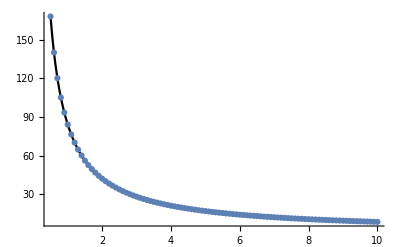

```mathematica
Show[Plot[-4π^2(π^2-12)/r,{r,0.5,10},PlotStyle->Black,PlotRange->All],ListPlot[v3Tab]]
```

```mathematica
BootstrapMeanStdDev[data_List,weights_List,nBootstrap_:1000]:=Module[{n,weightedData,resampledMeans,mean,stdDev},(*Ensure data and weights have the same length*)If[Length[data]≠Length[weights],Return[$Failed,Module]];
n=Length[data];
(*Combine data and weights*)weightedData=Transpose[{data,Abs[weights]}];
(*Function to resample data with replacement considering weights*)resampleWeightedData:=RandomChoice[weightedData[[All,2]]->weightedData,n];
(*Resample and calculate mean for each bootstrap sample*)resampledMeans=Mean[#[[All,1]]]&/@Table[resampleWeightedData,{nBootstrap}];
(*Calculate mean and standard deviation of the bootstrap means*)mean=Mean[resampledMeans];
stdDev=StandardDeviation[resampledMeans];
(*Return mean and standard deviation*){mean,stdDev}]






BootstrapMeanStdDevDifference[data1_List,weights1_List,data2_List,weights2_List,nBootstrap_:100]:=Module[{n1,n2,weightedData1,weightedData2,resampledMeans,mean,stdDev},(*Ensure data and weights have the same length for both datasets*)If[Length[data1]≠Length[weights1]||Length[data2]≠Length[weights2],Return[$Failed,Module]];
n1=Length[data1];
n2=Length[data2];
(*Combine data and weights for both datasets*)weightedData1=Transpose[{data1,weights1}];
weightedData2=Transpose[{data2,weights2}];
(*Function to resample data with replacement considering weights for both datasets*)resampleWeightedData:=Transpose[{RandomChoice[weightedData1[[All,2]]->weightedData1,n1][[All,1]],RandomChoice[weightedData2[[All,2]]->weightedData2,n2][[All,1]]}];
(*Resample and calculate mean of the difference for each bootstrap sample*)resampledMeans=Mean[#[[All,1]]-#[[All,2]]]&/@Table[resampleWeightedData,{nBootstrap}];
(*Calculate mean and standard deviation of the bootstrap means of differences*)mean=Mean[resampledMeans];
stdDev=StandardDeviation[resampledMeans];
(*Return mean and standard deviation of the differences*){mean,stdDev}]
```

## 2x2

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]

colorList={ColorData[97][1],ColorData[97][2],ColorData[9][2]}

Fig2legend=LineLegend[Table[colorList[[ii]],{ii,3}],{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{NNLO}'",Magnification->0.8]},LegendLayout->{"Column",3},LegendMargins->0.5,LegendFunction->frame]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.6745098039215687, 0.07450980392156863, 0.043137254901960784]}

```mathematica
dropboxDir="~/bassi/heavy_quark_nuclei/"
```

~/bassi/heavy_quark_nuclei/

```mathematica
HamALO=Import[dropboxDir<>"Hammys_LO_dtau4800.0_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.001_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac10.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]];
HamANLO=Import[dropboxDir<>"Hammys_NLO_dtau4800.0_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.001_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac10.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]];
HamANNLO=Import[dropboxDir<>"Hammys_NNLO_dtau4800.0_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.001_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac10.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]];

HamALOp=Import[dropboxDir<>"Hammys_LO_dtau4800.0_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.001_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_product_afac100000000.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]];
HamANLOp=Import[dropboxDir<>"Hammys_NLO_dtau4800.0_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.001_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_product_afac100000000.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]];
HamANNLOp=Import[dropboxDir<>"Hammys_NNLO_dtau4800.0_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.001_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_product_afac100000000.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]];
```

```mathematica
WALO=Import[dropboxDir<>"Hammys_LO_dtau4800.0_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.001_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac10.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]];
WANLO=Import[dropboxDir<>"Hammys_NLO_dtau4800.0_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.001_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac10.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]];
WANNLO=Import[dropboxDir<>"Hammys_NNLO_dtau4800.0_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.001_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac10.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]];
WALOp=Import[dropboxDir<>"Hammys_LO_dtau4800.0_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.001_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_product_afac100000000.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]];
WANLOp=Import[dropboxDir<>"Hammys_NLO_dtau4800.0_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.001_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_product_afac100000000.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]];
WANNLOp=Import[dropboxDir<>"Hammys_NNLO_dtau4800.0_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.001_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_product_afac100000000.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
matHamE1=Table[{BootstrapMeanStdDev[HamALO[[t]],WALO[[t]],100],BootstrapMeanStdDev[HamANLO[[t]],WANLO[[t]],100],BootstrapMeanStdDev[HamANNLO[[t]],WANNLO[[t]],100]},{t,1,2000}];
```

```mathematica
matHamE1[[All,1]][[1,2]]
```

8.68851×10^-12

```mathematica
(*Assuming yData is your list of 500 points like {{centralValue1,error1},{centralValue2,error2},...}*)(*Example:yData=Table[{RandomReal[{0,1}],RandomReal[{0.1,0.2}]},{500}];*)(*Generate taus*)taus=Table[t*4800,{t,1,2000}];

(*Preparing data for plotting*)
dataWithErrorsLO=Table[{taus[[i]],Around[matHamE1[[All,1]][[i,1]],matHamE1[[All,1]][[i,2]]]},{i,1,Length[taus]}];
dataWithErrorsNLO=Table[{taus[[i]],Around[matHamE1[[All,2]][[i,1]],matHamE1[[All,2]][[i,2]]]},{i,1,Length[taus]}];
dataWithErrorsNNLO=Table[{taus[[i]],Around[matHamE1[[All,3]][[i,1]],matHamE1[[All,3]][[i,2]]]},{i,1,Length[taus]}];
```

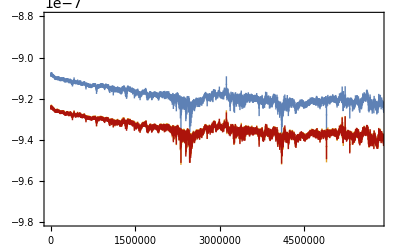

```mathematica
ΔEqqqqPlotmq=Legended[Legended[Show[ListPlot[dataWithErrorsLO,PlotRange->{{0,5800000},{-9.8*10^-7,-8.8 10^-7}},PlotStyle->ColorData[97][1]],ListPlot[dataWithErrorsNLO,PlotRange->{{0,5800000},{-9.8*10^-7,-8.8 10^-7}},PlotStyle->ColorData[97][2]],ListPlot[dataWithErrorsNNLO,PlotRange->{{0,5800000},{-9.8*10^-7,-8.8 10^-7}},PlotStyle->ColorData[9][2]],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX[" \\tau m_Q",Magnification->1.2],MaTeX["\\Delta E_{Q\\bar{Q}Q\\bar{Q}}(\\tau)/m_Q",Magnification->1.2]}],Placed[Fig2legend,{0.5,0.12}]],Placed[MaTeX["\\alpha_s=10^{-3}"],{0.87,0.91}]]
```

```mathematica
matHamE1p=Table[{BootstrapMeanStdDevDifference[HamALO[[t]],WALO[[t]],HamALOp[[t]],WALOp[[t]],100],BootstrapMeanStdDevDifference[HamANLO[[t]],WANLO[[t]],HamANLOp[[t]],WANLOp[[t]],100],BootstrapMeanStdDevDifference[HamANNLO[[t]],WANNLO[[t]],HamANNLOp[[t]],WANNLOp[[t]],100]},{t,1,2000}];
```

```mathematica
(*Assuming yData is your list of 500 points like {{centralValue1,error1},{centralValue2,error2},...}*)(*Example:yData=Table[{RandomReal[{0,1}],RandomReal[{0.1,0.2}]},{500}];*)(*Generate taus*)
taus=Table[t*4800,{t,1,2000}];
(*Preparing data for plotting*)
dataWithErrorsLOp=Table[{taus[[i]],Around[-matHamE1p[[All,1]][[i,1]],matHamE1p[[All,1]][[i,2]]]},{i,1,Length[taus]}];
dataWithErrorsNLOp=Table[{taus[[i]],Around[-matHamE1p[[All,2]][[i,1]],matHamE1p[[All,2]][[i,2]]]},{i,1,Length[taus]}];
dataWithErrorsNNLOp=Table[{taus[[i]],Around[-matHamE1p[[All,3]][[i,1]],matHamE1p[[All,3]][[i,2]]]},{i,1,Length[taus]}];
```

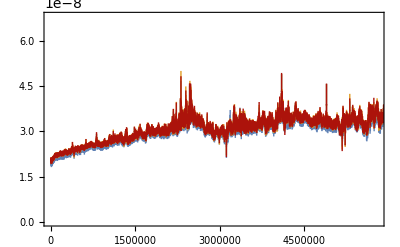

```mathematica
BEqqqqPlotmq=Legended[Legended[Show[ListPlot[dataWithErrorsLOp,PlotRange->{{0,5800000},{0,6.8 10^-8}},PlotStyle->ColorData[97][1]],ListPlot[dataWithErrorsNLOp,PlotRange->{{0,5800000},{0,6.8 10^-8}},PlotStyle->ColorData[97][2]],ListPlot[dataWithErrorsNNLOp,PlotRange->{{0,5800000},{0,6.8 10^-8}},PlotStyle->ColorData[9][2]],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX[" \\tau m_Q",Magnification->1.2],MaTeX["B_{Q\\bar{Q}Q\\bar{Q}}(\\tau)/m_Q",Magnification->1.2]}],Placed[Fig2legend,{0.5,0.12}]],Placed[MaTeX["\\alpha_s=10^{-3}"],{0.87,0.91}]]
```

```mathematica
HamALO=Around[Import[dropboxDir<>"Hammys_LO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac10.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]]];
HamANLO=Import[dropboxDir<>"Hammys_NLO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac10.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]];
HamANNLO=Import[dropboxDir<>"Hammys_NNLO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac10.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]];
HamALOp=Import[dropboxDir<>"Hammys_LO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_product_afac100000000.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]];
HamANLOp=Import[dropboxDir<>"Hammys_NLO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_product_afac100000000.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]];
HamANNLOp=Import[dropboxDir<>"Hammys_NNLO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_product_afac100000000.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]];
```

```mathematica
WALO=Import[dropboxDir<>"Hammys_LO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac10.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]];
WANLO=Import[dropboxDir<>"Hammys_NLO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac10.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]];
WANNLO=Import[dropboxDir<>"Hammys_NNLO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac10.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]];
WALOp=Import[dropboxDir<>"Hammys_LO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_product_afac100000000.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]];
WANLOp=Import[dropboxDir<>"Hammys_NLO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_product_afac100000000.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]];
WANNLOp=Import[dropboxDir<>"Hammys_NNLO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_product_afac100000000.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
WANLO//Length
```

501

```mathematica
matHamE1=Table[{BootstrapMeanStdDev[HamALO[[1,t]],WALO[[t]],100],BootstrapMeanStdDev[HamANLO[[t]],WANLO[[t]],100],BootstrapMeanStdDev[HamANNLO[[t]],WANNLO[[t]],100]},{t,1,500}];
```

```mathematica
taus=Table[t*0.4,{t,1,500}];
```

```mathematica
matHamE1[[All,1]][[1,2]]
```

8.68851×10^-12

```mathematica
matHamE1[[All,3]][[1,1]]
```

-0.0157423

```mathematica
(*Assuming yData is your list of 500 points like {{centralValue1,error1},{centralValue2,error2},...}*)(*Example:yData=Table[{RandomReal[{0,1}],RandomReal[{0.1,0.2}]},{500}];*)(*Generate taus*)taus=Table[t*0.4,{t,1,500}];

(*Preparing data for plotting*)
dataWithErrorsLO=Table[{taus[[i]],Around[matHamE1[[All,1]][[i,1]],matHamE1[[All,1]][[i,2]]]},{i,1,Length[taus]}];
dataWithErrorsNLO=Table[{taus[[i]],Around[matHamE1[[All,2]][[i,1]],matHamE1[[All,2]][[i,2]]]},{i,1,Length[taus]}];
dataWithErrorsNNLO=Table[{taus[[i]],Around[matHamE1[[All,3]][[i,1]],matHamE1[[All,3]][[i,2]]]},{i,1,Length[taus]}];
```

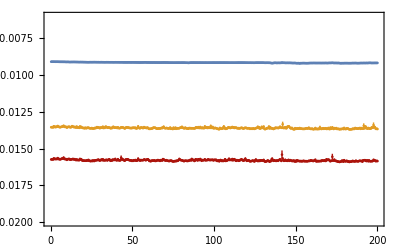

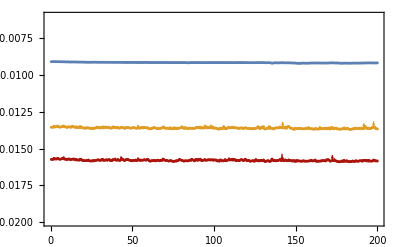

```mathematica
ΔEqqqqPlotmq=Legended[Legended[Show[ListPlot[dataWithErrorsLO,PlotRange->{{0,200},{-20*10^-3,-6*10^-3}},PlotStyle->ColorData[97][1]],ListPlot[dataWithErrorsNLO,PlotRange->{{0,200},{-20*10^-3,-6*10^-3}},PlotStyle->ColorData[97][2]],ListPlot[dataWithErrorsNNLO,PlotRange->{{0,200},{-20*10^-3,-6*10^-3}},PlotStyle->ColorData[9][2]],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX[" \\tau m_Q",Magnification->1.2],MaTeX["\\Delta E_{Q\\bar{Q}Q\\bar{Q}}(\\tau)/m_Q",Magnification->1.2]}],Placed[Fig2legend,{0.5,0.12}]],Placed[MaTeX["\\alpha_s=0.1"],{0.9,0.93}]]
```

```mathematica
matHamE1p=Table[{BootstrapMeanStdDevDifference[HamALO[[1,t]],WALO[[t]],HamALOp[[t]],WALOp[[t]],100],BootstrapMeanStdDevDifference[HamANLO[[t]],WANLO[[t]],HamANLOp[[t]],WANLOp[[t]],100],BootstrapMeanStdDevDifference[HamANNLO[[t]],WANNLO[[t]],HamANNLOp[[t]],WANNLOp[[t]],100]},{t,1,500}];
```

```mathematica
(*Assuming yData is your list of 500 points like {{centralValue1,error1},{centralValue2,error2},...}*)(*Example:yData=Table[{RandomReal[{0,1}],RandomReal[{0.1,0.2}]},{500}];*)(*Generate taus*)taus=Table[t*0.4,{t,1,500}];

(*Preparing data for plotting*)
dataWithErrorsLOp=Table[{taus[[i]],Around[-matHamE1p[[All,1]][[i,1]],matHamE1p[[All,1]][[i,2]]]},{i,1,Length[taus]}];
dataWithErrorsNLOp=Table[{taus[[i]],Around[-matHamE1p[[All,2]][[i,1]],matHamE1p[[All,2]][[i,2]]]},{i,1,Length[taus]}];
dataWithErrorsNNLOp=Table[{taus[[i]],Around[-matHamE1p[[All,3]][[i,1]],matHamE1p[[All,3]][[i,2]]]},{i,1,Length[taus]}];
```

```mathematica
dataWithErrorsNLOp[[1]]
```

{0.4,0.000450.00004}

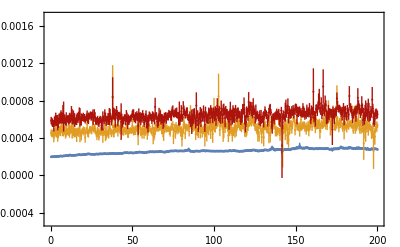

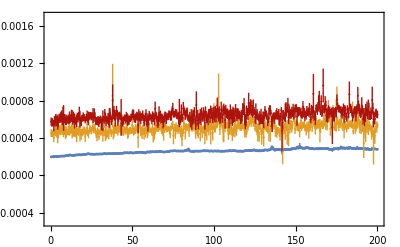

```mathematica
BEqqqqPlotmq=Legended[Legended[Show[ListPlot[dataWithErrorsLOp,PlotRange->{{0,200},{-0.0005,0.0017}},PlotStyle->ColorData[97][1]],ListPlot[dataWithErrorsNLOp,PlotRange->{{0,200},{-0.0005,0.0017}},PlotStyle->ColorData[97][2]],ListPlot[dataWithErrorsNNLOp,PlotRange->{{0,200},{-0.0005,0.0017}},PlotStyle->ColorData[9][2]],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX[" \\tau m_Q",Magnification->1.2],MaTeX["B_{Q\\bar{Q}Q\\bar{Q}}(\\tau)/m_Q",Magnification->1.2]}],Placed[Fig2legend,{0.5,0.12}]],Placed[MaTeX["\\alpha_s=0.1"],{0.87,0.91}]]
```

```mathematica
HamI1=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket20.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_I1.h5",{"Datasets","Hammys"}][[All,All,1]]
```

{{-0.0388288,-0.0378796,-0.039256,-0.0326763,-0.0312383,-0.0371432,-0.0328664,-0.03891,-0.0427955,-0.0343446,-0.041261,-0.0352431,-0.0375306,-0.0311602,9972,-0.0352492,-0.0445102,-0.0389954,-0.0349016,-0.0363893,-0.0380582,0.010713,-0.0466088,-0.0335564,-0.0312258,-0.0465905,-0.0161461,-0.0075631,-0.0438229},999,{1}}
 |  |  |  |

```mathematica
WI1=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket20.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_I1.h5",{"Datasets","Ws"}][[All,All,1]]
```

{{4.20555,7.27746,10.3117,6.26366,3.89611,6.39446,2.16444,6.90196,11.2051,3.50358,3.89114,4.20782,5.28951,3.49192,6.12441,3.72277,9968,3.48901,27.7533,5.17294,6.29094,8.4774,4.4433,4.66776,6.32563,1.44424,6.2758,4.54782,4.05183,3.58733,1.90593,1.71628,6.04006},999,{1}}
 |  |  |  |

```mathematica
HamI4=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket20.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_I4.h5",{"Datasets","Hammys"}][[All,All,1]]
```

{{-0.0388288,-0.0378796,-0.039256,-0.0326763,-0.0312383,-0.0371432,-0.0328664,-0.03891,-0.0427955,-0.0343446,-0.041261,-0.0352431,-0.0375306,-0.0311602,9972,-0.0352492,-0.0445102,-0.0389954,-0.0349016,-0.0363893,-0.0380582,0.010713,-0.0466088,-0.0335564,-0.0312258,-0.0465905,-0.0161461,-0.0075631,-0.0438229},999,{1}}
 |  |  |  |

```mathematica
WI4=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket20.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_I4.h5",{"Datasets","Ws"}][[All,All,1]]
```

{{17.6867,52.9614,106.331,39.2335,15.1796,40.8891,4.68479,47.637,125.555,12.2751,15.1409,17.7057,27.9789,12.1935,37.5084,13.859,9968,12.1732,770.243,26.7593,39.5759,71.8664,19.7429,21.788,40.0136,2.08581,39.3856,20.6827,16.4174,12.8689,3.63255,2.94561,36.4824},999,{1}}
 |  |  |  |

```mathematica
WI4[[1]]
```

```mathematica
HamI1[[1]]/HamA[[1]]
```

```mathematica
Dimensions[WA]
```

{1001,10000}

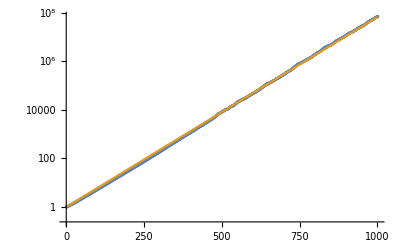

```mathematica
Show[ListLogPlot[Table[Mean[WA[[τ]]],{τ,1,1001}]],LogPlot[Exp[-(-.045)τ .4],{τ,0,1001},PlotStyle->ColorData[97][2]]]
```

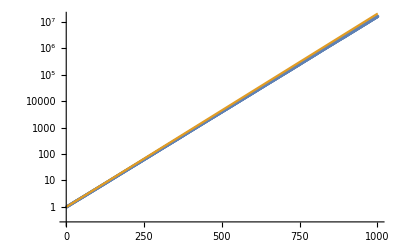

```mathematica
Show[ListLogPlot[Table[Mean[WB[[τ]]],{τ,1,1001}]],LogPlot[Exp[-(-.042)τ .4],{τ,0,1001},PlotStyle->ColorData[97][2]]]
```

```mathematica
fac=Mean[WI1[[1]]]/Sqrt[Mean[WI4[[1]]]]
```

0.426966

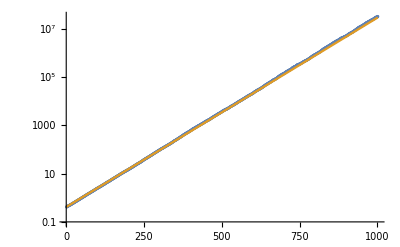

```mathematica
Show[ListLogPlot[Table[Mean[WI1[[τ]]]/Sqrt[Mean[WI4[[1]]]],{τ,1,1001}]],LogPlot[fac Exp[-(-.045)τ .4],{τ,0,1001},PlotStyle->ColorData[97][2]]]
```

```mathematica
mat=Table[{{Mean[WA[[τ]]],Mean[WI1[[τ]]]/Sqrt[Mean[WI4[[1]]]]},{Mean[WI1[[τ]]]/Sqrt[Mean[WI4[[1]]]],Mean[WB[[τ]]]}},{τ,1,1001}];
```

```mathematica
mat=Table[{{Mean[WA[[τ]]],Mean[WI1[[τ]]]/Sqrt[Mean[WI4[[τ]]]]},{Mean[WI1[[τ]]]/Sqrt[Mean[WI4[[τ]]]],Mean[WB[[τ]]]}},{τ,1,1001}];
```

```mathematica
matHam=Table[{{Mean[WA[[τ]]HamA[[τ]]]/Mean[WA[[τ]]],Mean[HamI1[[τ]]WI1[[τ]]]/Mean[WI1[[τ]]]},{Mean[HamI1[[τ]]WI1[[τ]]]/Mean[WI1[[τ]]],Mean[WB[[τ]]HamB[[τ]]]/Mean[WB[[τ]]]}},{τ,1,1001}];
```

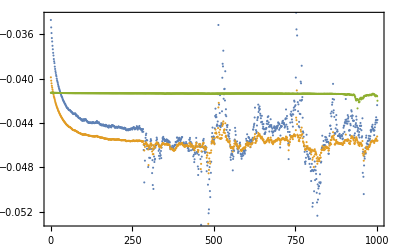

```mathematica
ListPlot[{matHam[[All,1,1]],matHam[[All,1,2]],matHam[[All,2,2]]},Frame->True]
```

```mathematica
NMeas=Length[WA[[1]]]
```

10000

```mathematica
NBoot=200;
```

```mathematica
bootIndices=RandomInteger[{1,NMeas},{NBoot,NMeas}];
```

```mathematica
Dimensions[bootIndices]
```

{200,10000}

```mathematica
bootmat=ParallelTable[Print[b];Table[{{Mean[WA[[τ,bootIndices[[b]]]]],
Mean[WI1[[τ,bootIndices[[b]]]]]/Sqrt[Mean[WI4[[τ,bootIndices[[b]]]]]]},{Mean[WI1[[τ,bootIndices[[b]]]]]/Sqrt[Mean[WI4[[τ,bootIndices[[b]]]]]],
Mean[WB[[τ,bootIndices[[b]]]]]}},{τ,1,1001}],{b,1,NBoot}];
```

1

10

19

28

37

46

2

47

11

20

38

29

3

48

12

21

30

39

4

49

22

40

31

13

5

50

23

32

41

14

24

33

51

42

6

15

25

34

52

7

43

16

26

35

53

44

8

17

27

36

Null

Null

Null

«135 more identical outputs»

198

159

175

183

191

168

199

160

176

184

200

192

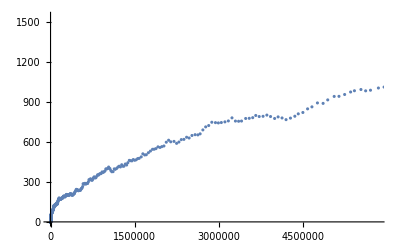

```mathematica
ListPlot[bootmat[[1,All,1]]]
```

```mathematica
t0=100;tref=220;
```

```mathematica
Timing[{evals,evecs}=Eigensystem[{mat[[tref]],mat[[t0]]}]]
```

{0.010264,{{8.94502,6.95328},{{-0.848818,0.528685},{-0.443305,-0.896371}}}}

```mathematica
{evals,evecs}=Eigensystem[{mat[[tref]],mat[[t0]]}]
```

{{8.94502,6.95328},{{-0.848818,0.528685},{-0.443305,-0.896371}}}

```mathematica
{evals,evecs}=Eigensystem[{mat[[tref]],mat[[t0]]}]
```

{{8.94502,6.95328},{{-0.848818,0.528685},{-0.443305,-0.896371}}}

```mathematica
t0s=Table[Table[t0,{tref,t0+50,1000,50}],{t0,100,950,50}];
```

```mathematica
tRs=Table[Table[tref,{tref,t0+50,1000,50}],{t0,100,950,50}];
```

```mathematica
eigenSys=Table[Table[Eigensystem[{mat[[tref]],mat[[t0]]}],{tref,t0+50,1000,50}],{t0,100,950,50}];
```

```mathematica
booteigenSys=ParallelTable[Table[Table[Eigensystem[{bootmat[[b,tref]],bootmat[[b,t0]]}],{tref,t0+50,1000,50}],{t0,100,950,50}],{b,1,NBoot}];
```

```mathematica
eigenVecs=eigenSys[[All,All,2]];
```

```mathematica
eigenVals=eigenSys[[All,All,1]];
```

```mathematica
booteigenVecs=booteigenSys[[All,All,All,2]];
```

```mathematica
UQ=(1+Erf[1/Sqrt[2.]])/2;
LQ=(1-Erf[1/Sqrt[2.]])/2;
```

```mathematica
CI[boots_]:=Block[{LQ,UQ,upper,lower},
UQ=(1+Erf[1/Sqrt[2.]])/2;
LQ=(1-Erf[1/Sqrt[2.]])/2;
upper=Quantile[boots,UQ];
lower=Quantile[boots,LQ];
(upper-lower)/2];
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

Null

Null

Null

«146 more identical outputs»

136

128

152

153

161

169

177

185

193

154

162

170

163

178

186

194

155

171

164

179

172

187

195

156

165

180

188

173

196

157

166

181

189

174

197

158

167

198

190

175

182

168

159

191

176

199

183

Null

Null

Null

«1 more identical outputs»

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

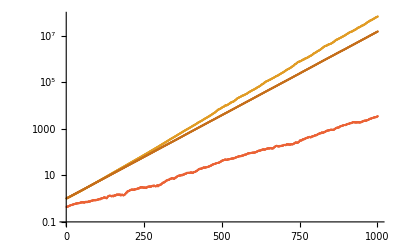

```mathematica
Null
```

```mathematica
eigen3pt=Table[Table[(cMat.matHam3pt[[τ]].Transpose[cMat])[[n,n]],{τ,1,Length[mat]}],{n,2}];
```

```mathematica
eigen2pt=Table[Table[(cMat.mat[[τ]].Transpose[cMat])[[n,n]],{τ,1,Length[mat]}],{n,2}];
```

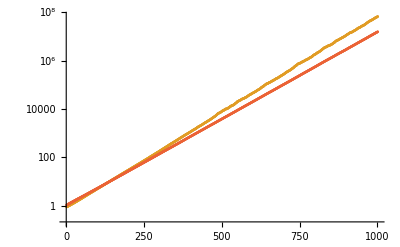

```mathematica
ListLogPlot[{eigen3pt[[1]],eigen2pt[[1]],eigen3pt[[2]],eigen2pt[[2]]}]
```

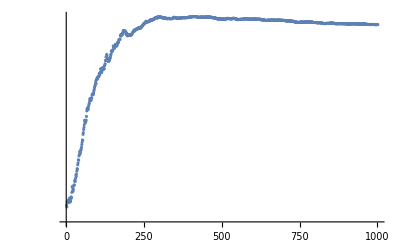

```mathematica
ListLogPlot[{eigen2pt[[1]]/mat[[All,1,1]]}]
```

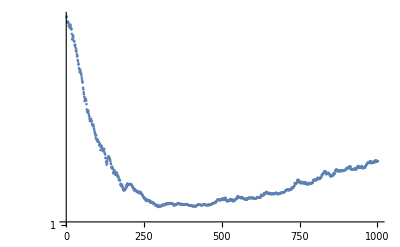

```mathematica
ListLogPlot[{eigen2pt[[2]]/mat[[All,2,2]]}]
```

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

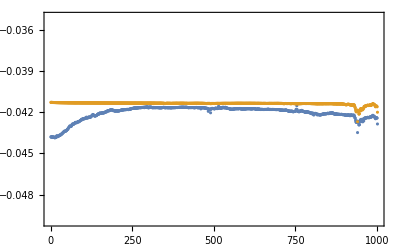

```mathematica
Null
```

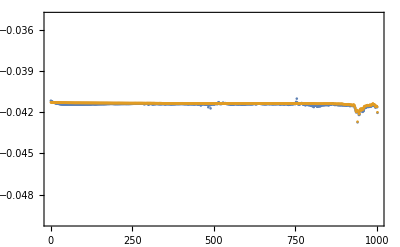

```mathematica
ListPlot[{eigen3pt[[2]]/eigen2pt[[2]],matHam3pt[[All,2,2]]/(mat[[All,2,2]])},Frame->True,PlotRange->{-.05,-.035}]
```

```mathematica
thresh=-(0.21485 4/3)^2/2
```

-0.0410316

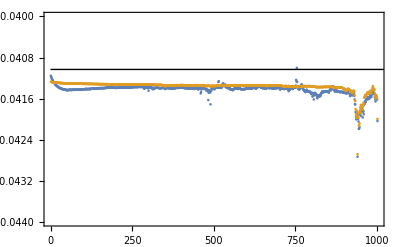

```mathematica
Show[ListPlot[{eigen3pt[[2]]/eigen2pt[[2]],matHam3pt[[All,2,2]]/(mat[[All,2,2]])},Frame->True,PlotRange->{-.044,-.04}],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}]]
```

```mathematica
eigenHam=Table[eigen3pt[[n]]/eigen2pt[[n]],{n,2}];
```

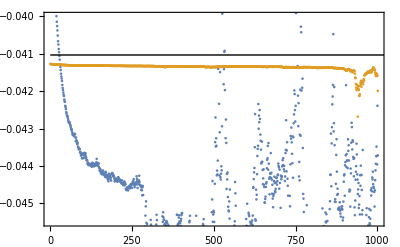

```mathematica
Show[ListPlot[{matHam[[All,1,1]],matHam[[All,2,2]]},Frame->True],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}],PlotRange->{{1,1000},{-.0455,-.04}}]
```

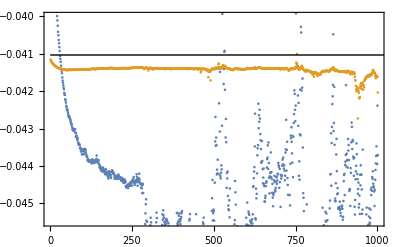

```mathematica
Show[ListPlot[{eigenHam[[1]],eigenHam[[2]]},Frame->True],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}],PlotRange->{{1,1000},{-.0455,-.04}}]
```

```mathematica
stop={500,1001};
```

```mathematica
matHamEM=Table[Table[{(τ-1).4,Around[matHam3pt[[τ,n,n]]/mat[[τ,n,n]],CI[bootmatHam3pt[[All,τ,n,n]]/bootmat[[All,τ,n,n]]]]},{τ,stop[[n]]}],{n,2}];
```

```mathematica
boott0I=RandomInteger[{1,10},NBoot]
```

{6,2,1,8,2,6,4,2,9,2,5,6,3,3,6,2,7,5,10,2,10,6,4,3,9,4,10,6,9,7,3,10,5,10,8,7,1,2,4,4,9,6,1,7,10,4,1,7,9,2,9,1,5,2,4,3,2,5,10,8,9,7,4,8,10,4,2,8,2,5,2,6,5,2,3,10,7,9,9,9,5,7,7,5,3,5,3,1,10,10,4,7,4,4,6,5,3,2,2,1,6,9,6,5,4,3,8,2,4,5,8,5,7,5,2,10,10,3,6,9,9,7,7,6,8,4,6,10,4,4,9,6,8,3,5,1,3,8,4,10,3,5,7,5,2,3,9,6,2,8,1,8,6,2,6,5,1,3,9,10,7,2,2,5,7,9,5,2,5,7,10,3,2,1,8,9,1,5,3,3,10,8,3,4,4,8,3,3,7,5,3,1,5,8,7,7,3,7,10,1}

```mathematica
boottRI=Table[RandomInteger[{1,Length[booteigenVecs[[1,boott0I[[b]]]]]}],{b,NBoot}]
```

{1,16,7,1,1,11,6,15,5,7,13,13,15,6,11,12,8,1,3,7,5,2,11,9,10,9,9,7,2,4,5,4,12,4,1,4,4,5,4,14,2,13,8,10,1,11,4,3,6,5,10,12,14,6,2,4,5,4,2,9,8,11,2,9,2,12,6,3,10,6,12,7,10,6,12,3,11,2,2,2,6,7,5,13,10,1,16,2,3,7,14,7,9,4,9,6,13,3,16,8,12,6,3,11,12,2,11,15,10,13,9,9,9,9,11,2,3,15,12,5,10,6,11,6,4,8,5,8,12,14,6,9,7,8,13,8,6,10,13,9,6,13,8,7,2,14,9,1,12,10,17,3,13,1,1,13,4,5,2,7,5,7,14,8,1,5,3,17,14,1,9,10,5,3,11,8,15,2,10,14,4,9,16,10,5,11,14,12,4,4,2,16,14,8,5,2,12,2,2,1}

```mathematica
-Re[Table[booteigenVecs[[b,boott0I[[b]],boottRI[[b]],1,1]],{b,2}]]
```

{0.992093,0.995004}

```mathematica
Dimensions[booteigenVecs]
```

{200,18}

```mathematica
Dimensions[booteigenVecs[[All,3]]]
```

{200,16,2,2}

```mathematica
bootc11=-Re[Table[booteigenVecs[[b,boott0I[[b]],boottRI[[b]],1,1]],{b,NBoot}]];
```

```mathematica
bootc12=-Re[Table[booteigenVecs[[b,boott0I[[b]],boottRI[[b]],1,2]],{b,NBoot}]];
```

```mathematica
bootc21=-Re[Table[booteigenVecs[[b,boott0I[[b]],boottRI[[b]],2,1]],{b,NBoot}]];
```

```mathematica
bootc22=-Re[Table[booteigenVecs[[b,boott0I[[b]],boottRI[[b]],2,2]],{b,NBoot}]];
```

```mathematica
bootcMat=Table[{{bootc11[[b]],bootc12[[b]]},{bootc21[[b]],bootc22[[b]]}},{b,NBoot}];
```

```mathematica
booteigen3pt=Table[Table[Table[(cMat.bootmatHam3pt[[b,τ]].Transpose[cMat])[[n,n]],{τ,1,Length[mat]}],{n,2}],{b,NBoot}];
```

```mathematica
booteigen2pt=Table[Table[Table[(cMat.bootmat[[b,τ]].Transpose[cMat])[[n,n]],{τ,1,Length[mat]}],{n,2}],{b,NBoot}];
```

```mathematica
booteigen3pt=Table[Table[Table[(bootcMat[[b]].bootmatHam3pt[[b,τ]].Transpose[bootcMat[[b]]])[[n,n]],{τ,1,Length[mat]}],{n,2}],{b,NBoot}];
```

```mathematica
booteigen2pt=Table[Table[Table[(bootcMat[[b]].bootmat[[b,τ]].Transpose[bootcMat[[b]]])[[n,n]],{τ,1,Length[mat]}],{n,2}],{b,NBoot}];
```

```mathematica
booteigenHam=Table[Table[booteigen3pt[[b,n]]/booteigen2pt[[b,n]],{n,2}],{b,NBoot}];
```

```mathematica
eigenHamEM=Table[Table[{(τ-1).4,Around[eigenHam[[n,τ]],CI[booteigenHam[[All,n,τ]]]]},{τ,stop[[n]]}],{n,2}];
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
<<MaTeX`
```

```mathematica
TrimBleed[p2_]:=Show[p2,With[{d=.2},Graphics[{White,FilledCurve[{{Line[ImageScaled/@{{-d,-d},{-d,1+d},{1+d,1+d},{1+d,-d}}]},{Line[Scaled/@{{0,0},{0,1},{1,1},{1,0}}]}}]}]],ImagePadding->{{70,10},{45,10}}]
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
origlegend=PointLegend[Table[Directive[ColorData[97][ii]],{ii,2}],{MaTeX["b/a=5",Magnification->0.8],MaTeX["b/a=100",Magnification->0.8]},LegendMarkers->Table[Automatic,{ii,2}],LegendLayout->{"Column",4},LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
EMPorig=TrimBleed[Show[ListPlot[matHamEM,Joined->False,Frame->True,PlotLegends->Placed[origlegend,{.75,.2}]],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}],PlotRange->{{1,1000 .4},{-.05,-.04}},BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],Frame->True,Axes->False,GridLines->{{0},{0}},FrameLabel->{MaTeX["\\tau \\ m_Q",Magnification->1.2],MaTeX["\\left<\\Psi_T|H(\\tau)|\\Psi_T \\right> / m_Q",Magnification->1.2]}]]
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

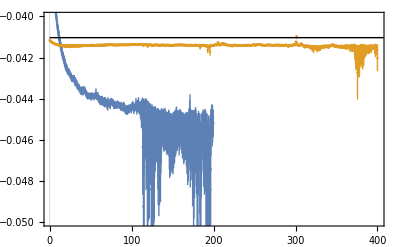

```mathematica
Null
```

```mathematica
Export[dropboxDir<>"/physics/projects/heavy_quark_nuclei/EMGEVP.pdf",EMPGEVP]
```

~/Dropbox//physics/projects/heavy_quark_nuclei/EMGEVP.pdf

```mathematica
GEVPlegend=PointLegend[Table[Directive[ColorData[97][ii+2]],{ii,2}],{MaTeX["n=0",Magnification->0.8],MaTeX["n=1",Magnification->0.8]},LegendMarkers->Table[Automatic,{ii,2}],LegendLayout->{"Column",4},LegendMargins->0.5,LegendFunction->frame]
```

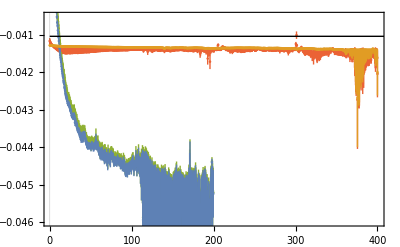

```mathematica
EMboth=Show[ListPlot[eigenHamEM,Joined->False,Frame->True,PlotLegends->Placed[GEVPlegend,{.725,.2}],PlotStyle->{ColorData[97][3],ColorData[97][4]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][4]}],ListPlot[matHamEM,Joined->False,Frame->True,PlotLegends->Placed[origlegend,{.77,.3}]],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}],PlotRange->{{1,1000 .4},{-.049,-.0405}},BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],Frame->True,Axes->False,GridLines->{{0},{0}},FrameLabel->{MaTeX["\\tau \\ m_Q",Magnification->1.2],MaTeX["\\Delta E_n(\\tau) / m_Q",Magnification->1.2]}]
```

```mathematica
Export[dropboxDir<>"/physics/projects/heavy_quark_nuclei/EMboth.pdf",EMboth]
```

~/Dropbox//physics/projects/heavy_quark_nuclei/EMboth.pdf

```mathematica
eigenHamEM[[1,250]]
```

{99.6,-0.044530.00019}

```mathematica
eigenHamEM[[2,250]]
```

{99.6,-0.041380.00005}

```mathematica
eigenHamEM[[1,250,2]]-thresh
```

-0.003500.00019

```mathematica
eigenHamEM[[2,250,2]]-thresh
```

-0.000350.00005

```mathematica
mb=4.77050;
```

```mathematica
Mean[(eigenHamEM[[1,200;;350,2]]-thresh)]mb 1000
```

-20.40.6

```mathematica
0.281402*4
```

1.12561

```mathematica
.214850^2(4/3)^2/4/4
```

0.00512895

```mathematica
(eigenHamEM[[2,250;;,2]]-thresh)mb 1000
```

{-1.650.24,-1.650.23,-1.650.23,-1.640.22,-1.640.22,-1.630.22,-1.640.23,-1.630.24,-1.630.24,-1.630.23,-1.630.23,-1.630.22,-1.630.22,-1.640.22,-1.630.21,-1.630.21,-1.630.22,-1.630.22,-1.620.22,-1.630.22,-1.630.22,-1.610.22,-1.610.21,-1.620.21,-1.630.23,-1.620.22,-1.620.21,-1.620.21,-1.620.22,-1.620.21,-1.620.21,-1.630.21,-1.620.20,-1.620.21,-1.630.21,-1.690.23,-1.670.22,-1.800.31,-1.660.22,-1.720.26,-1.660.21,-1.660.21,-1.650.21,-1.640.20,-1.640.21,-1.670.22,-1.640.21,-1.660.22,-1.680.23,-1.740.26,-2.00.5,-1.670.21,-1.700.22,-1.670.21,-1.680.22,-1.710.23,-1.650.21,-1.640.20,-1.660.20,-1.690.22,-1.680.21,-1.780.27,-1.740.24,-1.820.31,-1.760.25,-1.840.32,-1.690.21,-1.720.24,-1.740.24,-1.740.24,-1.750.23,-1.710.21,-1.710.21,-1.700.22,-1.680.22,-1.670.22,-1.680.23,-1.700.23,-1.700.23,-1.690.23,-1.700.22,-1.730.23,-1.740.24,-1.720.22,-1.750.24,-1.730.23,-1.740.24,-1.740.24,-1.730.23,-1.760.25,-1.720.23,-1.710.23,-1.710.22,-1.700.22,-1.710.21,-1.690.22,-1.690.23,-1.730.23,-1.710.22,-1.770.23,-1.740.23,-1.830.28,-1.760.23,-1.770.23,-1.740.22,-1.720.22,-1.720.22,-1.730.23,-1.710.22,-1.740.22,-1.730.22,-1.720.22,-1.740.22,-1.750.22,-1.730.21,-1.720.22,-1.750.23,-1.780.24,-1.790.24,-1.780.24,-1.780.24,-1.790.25,-1.770.25,-1.750.24,-1.750.24,-1.760.24,-1.760.24,-1.760.24,-1.750.22,-1.740.23,-1.740.23,-1.740.22,-1.750.22,-1.720.23,-1.710.23,-1.720.22,-1.710.23,-1.690.21,-1.700.21,-1.720.23,-1.720.23,-1.710.22,-1.710.23,-1.710.23,-1.700.22,-1.710.23,-1.700.23,-1.690.22,-1.690.22,-1.690.21,-1.690.22,-1.690.22,-1.680.22,-1.680.22,-1.700.23,-1.700.23,-1.700.23,-1.710.22,-1.700.22,-1.710.23,-1.730.23,-1.740.22,-1.730.22,-1.740.23,-1.720.22,-1.720.22,-1.730.22,-1.710.22,-1.740.22,-1.760.21,-1.770.22,-1.770.23,-1.780.24,-1.780.23,-1.790.24,-1.720.21,-1.730.21,-1.720.21,-1.730.22,-1.740.22,-1.770.24,-1.750.23,-1.730.23,-1.750.23,-1.740.23,-1.760.23,-1.760.23,-1.790.24,-1.750.23,-1.770.24,-1.810.25,-1.800.25,-1.760.23,-1.770.24,-1.730.23,-1.730.23,-1.700.20,-1.710.21,-1.750.24,-1.760.25,-1.760.24,-1.820.27,-1.860.30,-1.830.28,-1.770.25,-1.740.22,-1.740.23,-1.740.22,-1.740.23,-1.800.25,-2.20.6,-2.10.5,-1.860.30,-1.800.24,-1.780.25,-1.760.24,-1.750.22,-1.740.22,-1.740.22,-1.740.22,-1.790.24,-1.820.24,-1.790.24,-1.820.25,-1.800.23,-1.840.25,-1.840.26,-1.810.24,-1.980.33,-1.890.30,-1.900.30,-1.880.29,-2.00.4,-2.81.3,-2.20.5,-2.10.5,-2.00.4,-1.940.32,-2.10.4,-2.10.5,-3.21.7,-1.980.34,-1.970.31,-1.800.24,-1.770.23,-1.750.21,-1.740.20,-1.810.24,-1.790.22,-1.780.23,-1.780.23,-1.810.24,-1.850.26,-1.750.21,-1.660.19,-1.630.20,-1.680.19,-1.660.21,-1.660.19,-1.710.21,-1.700.20,-1.700.21,-1.680.20,-1.540.23,-1.20.6,-1.10.7,-1.590.21,-1.710.21,-1.630.20,-1.550.24,-1.700.20,-1.710.20,-1.690.20,-1.680.20,-1.690.21,-1.610.20,-1.440.29,-1.40.4,-1.40.4,-1.30.4,-1.540.22,-1.520.24,-1.490.25,-1.490.26,-1.550.21,-1.400.32,-1.620.19,-1.590.20,-1.630.19,-1.700.21,-1.680.21,-1.690.22,-1.680.21,-1.720.22,-1.740.21,-1.740.22,-1.750.22,-1.740.21,-1.760.23,-1.720.21,-1.820.27,-1.890.31,-1.890.33,-1.850.31,-1.850.30,-1.830.28,-1.850.31,-1.850.31,-1.90.4,-1.880.32,-1.860.32,-1.820.28,-1.830.28,-1.770.25,-1.760.25,-1.690.22,-1.700.22,-1.720.24,-1.770.26,-1.770.26,-1.780.26,-1.750.25,-1.780.27,-1.790.27,-1.810.28,-1.800.28,-1.800.28,-1.780.27,-1.770.26,-1.760.25,-1.750.25,-1.770.26,-1.820.29,-1.830.29,-1.840.30,-1.850.31,-1.840.30,-1.840.29,-1.830.29,-1.830.29,-1.840.30,-1.820.28,-1.810.27,-1.820.28,-1.830.28,-1.840.29,-1.810.27,-1.810.28,-1.780.27,-1.740.25,-1.760.25,-1.780.26,-1.720.23,-1.760.25,-1.760.26,-1.780.26,-1.730.23,-1.730.23,-1.740.24,-1.750.25,-1.760.26,-1.740.25,-1.790.27,-1.750.25,-1.770.26,-1.760.25,-1.760.25,-1.750.25,-1.760.25,-1.750.24,-1.700.21,-1.700.21,-1.680.21,-1.670.21,-1.660.22,-1.630.23,-1.580.25,-1.770.26,-1.770.26,-1.720.23,-1.750.24,-1.740.23,-1.690.22,-1.650.22,-1.640.21,-1.640.20,-1.570.25,-1.610.22,-1.580.24,-1.600.23,-1.590.24,-1.600.23,-1.630.22,-1.650.22,-1.670.24,-1.700.23,-1.690.22,-1.650.25,-1.700.24,-1.720.24,-1.750.25,-1.730.25,-1.700.24,-1.740.27,-1.730.26,-1.770.26,-1.760.26,-1.760.27,-1.750.26,-1.740.26,-1.770.28,-1.750.26,-1.730.26,-1.710.25,-1.700.25,-1.670.25,-1.720.25,-1.670.26,-1.690.23,-1.720.24,-1.750.26,-1.720.24,-1.710.24,-1.720.24,-1.680.22,-1.730.24,-1.710.23,-1.720.24,-1.760.26,-1.740.24,-1.760.26,-1.780.27,-1.760.25,-1.750.25,-1.730.23,-1.720.24,-1.730.24,-1.750.25,-1.750.26,-1.750.26,-1.730.25,-1.720.25,-1.720.25,-1.740.25,-1.720.24,-1.710.24,-1.710.24,-1.690.22,-1.700.22,-1.700.24,-1.750.27,-1.720.25,-1.740.26,-1.90.4,-1.800.32,-1.740.28,-1.750.26,-1.740.26,-1.750.25,-1.730.25,-1.730.24,-1.750.24,-1.760.24,-1.780.26,-1.800.25,-1.780.26,-1.830.29,-1.790.27,-1.770.26,-1.720.27,-1.710.28,-1.660.31,-1.770.25,-1.740.27,-1.740.27,-1.800.28,-1.810.28,-1.840.30,-1.910.33,-2.00.4,-1.90.4,-1.910.35,-1.850.34,-1.880.31,-1.800.31,-1.740.29,-1.790.33,-1.740.33,-1.750.29,-1.760.27,-1.770.29,-1.710.29,-1.820.33,-1.730.34,-1.690.34,-1.690.32,-1.60.4,-1.70.4,-1.70.4,-1.710.32,-1.70.4,-1.50.5,-1.01.0,-1.10.9,0.12.2,-1.20.8,-1.60.4,-1.70.4,-1.80.4,-1.680.35,-1.860.32,-1.820.29,-1.860.31,-1.760.30,-1.70.4,-1.750.30,-1.50.5,-1.50.5,-1.630.34,-1.40.6,-1.610.35,-1.580.35,-1.740.25,-1.840.30,-1.850.30,-1.880.30,-1.90.4,-1.90.4,-2.00.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.00.4,-1.880.31,-2.00.4,-2.00.4,-1.970.35,-2.00.4,-2.00.4,-2.00.4,-2.10.4,-2.10.4,-2.10.5,-2.00.4,-2.10.4,-2.20.5,-2.20.5,-2.30.6,-2.20.5,-2.20.5,-2.20.6,-2.50.8,-2.50.7,-2.20.5,-2.20.5,-2.81.0,-2.40.7,-2.20.5,-2.20.5,-2.30.6,-2.20.5,-2.30.5,-2.30.5,-2.30.6,-2.40.7,-2.60.7,-2.70.9,-2.40.6,-2.50.7,-2.40.6,-2.40.6,-2.50.6,-2.40.6,-2.50.7,-2.40.6,-2.40.6,-2.40.6,-2.30.5,-2.30.5,-2.20.4,-2.10.4,-2.00.4,-2.10.4,-2.10.4,-2.10.4,-2.00.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.00.4,-2.10.4,-2.00.4,-2.00.4,-2.10.4,-2.00.4,-2.00.4,-2.00.4,-2.00.4,-2.00.4,-2.10.5,-2.10.5,-2.10.4,-2.00.4,-2.00.4,-1.90.4,-1.90.4,-1.80.4,-1.90.4,-1.80.4,-1.80.4,-1.70.4,-1.70.5,-1.70.5,-1.60.6,-1.80.4,-1.80.5,-1.70.5,-1.90.4,-2.00.4,-2.00.4,-2.00.4,-2.00.4,-1.90.4,-1.90.4,-2.00.4,-2.00.4,-2.00.4,-2.00.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.20.5,-2.10.4,-2.10.4,-2.10.4,-2.10.5,-2.20.5,-2.10.5,-2.10.5,-2.20.5,-2.00.7,-2.20.5,-2.20.5,-2.20.6,-2.20.5,-2.10.4,-2.00.5,-2.00.4,-2.00.5,-2.10.5,-2.20.5,-2.20.5,-2.30.5,-2.50.7,-2.30.6,-2.30.6,-2.20.7,-2.10.6,-2.20.7,-2.40.8,-2.40.8,-2.30.7,-2.30.7,-2.20.6,-2.30.7,-2.20.6,-2.50.7,-2.81.0,-3.21.4,-3.21.4,-3.92.1,-4.42.6,-4.62.8,-4.52.7,-4.12.2,-4.22.3,-8.6.,-4.32.4,-4.62.7,-4.82.9,-6.4.,-6.4.,-5.43.4,-4.22.3,-3.81.9,-4.02.2,-3.61.7,-4.32.4,-3.91.9,-3.71.7,-3.81.8,-3.51.7,-4.52.3,-4.01.9,-3.91.8,-4.22.1,-3.31.4,-3.21.3,-3.21.3,-2.91.1,-3.01.2,-3.01.1,-2.81.0,-2.81.0,-2.80.9,-2.80.9,-2.70.9,-2.60.8,-2.60.8,-2.80.9,-2.70.9,-2.60.9,-2.71.0,-2.60.8,-2.50.7,-2.40.7,-2.50.8,-2.60.8,-2.60.8,-2.40.7,-2.20.5,-2.20.5,-2.00.4,-1.90.5,-2.00.4,-2.20.4,-2.30.5,-2.20.5,-2.30.5,-2.60.8,-2.81.0,-3.01.1,-2.70.9,-2.60.9,-2.70.9,-2.81.0,-2.81.2,-4.82.9}

```mathematica
eigenHamEM[[2]]
```

Null

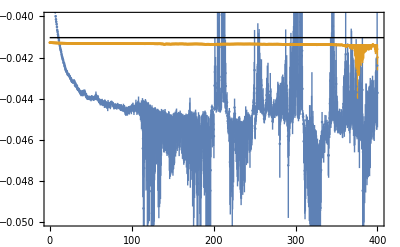

```mathematica
Show[ListPlot[matHamEM,Joined->False,Frame->True],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}],PlotRange->{{1,1000 .4},{-.05,-.04}}]
```

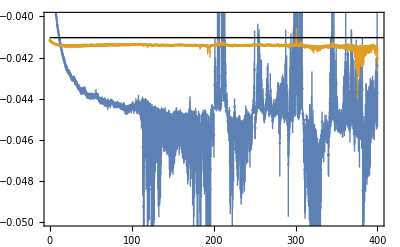

```mathematica
Show[ListPlot[eigenHamEM,Joined->False,Frame->True],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}],PlotRange->{{1,1000 .4},{-.05,-.04}}]
```

```mathematica
matHam[[1]]
```

{{-0.0347258,-0.0398865},{-0.0398865,-0.041273}}

```mathematica
matmatHam[[1000]]
```

{{-2.86816×10^6,-1.3933×10^6},{-1.3933×10^6,-637145.}}

```mathematica
Table[cMat.mat[[τ]].matHam[[τ]].Transpose[mat[[τ]]].Transpose[cMat],{τ,1,1}]
```

{{{-0.0301529,-0.0328281},{-0.0328281,-0.0334712}}}

```mathematica
Table[Transpose[cMat].Transpose[mat[[τ]]].matHam[[τ]].cMat.mat[[τ]],{τ,1,1}]
```

{{{-0.0294753,-0.0327108},{-0.0328664,-0.0341525}}}

```mathematica
Table[cMat.mat[[τ]].matHam[[τ]],{τ,1,1}]
```

{{{-0.0323821,-0.036749},{-0.0355931,-0.037185}}}

```mathematica
Table[Transpose[cMat].Transpose[mat[[τ]]].matHam[[τ]],{τ,1,1}]
```

{{{-0.0319791,-0.0363195},{-0.0359744,-0.0376087}}}

```mathematica
mat
```

```mathematica
matHam[[1]]
```

{{-0.0347258,-0.0398865},{-0.0398865,-0.041273}}

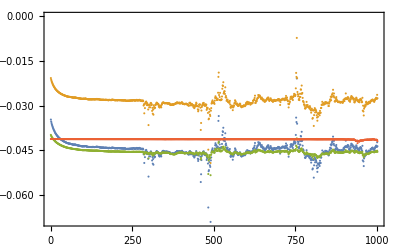

```mathematica
ListPlot[{ matHam[[All,1,1]],c11[[1]] matHam[[All,1,1]]+c12[[1]] matHam[[All,1,2]],matHam[[All,1,2]],matHam[[All,2,2]]},Frame->True]
```

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{-0.430897,-0.296194,-0.536342,-0.531442,-0.52827,-0.492685,-0.491518,-0.528522,0.742784,-0.427323,-0.402003,«30»,-0.483738,-0.29733,-0.447551,-0.35939,-0.5671,-0.580002,-0.50034,-0.324017,-0.409612,«150»},«19»].

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{-0.430897,-0.296194,-0.536342,-0.531442,-0.52827,-0.492685,-0.491518,-0.528522,0.742784,-0.427323,-0.402003,«30»,-0.483738,-0.29733,-0.447551,-0.35939,-0.5671,-0.580002,-0.50034,-0.324017,-0.409612,«150»},«20»].

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{-0.404763,-0.865885-0.0448084 ⅈ,-0.095352,-0.182075,0.0499562,0.0103266,-0.167085,-0.149282,-0.195281,-0.34269,«31»,-0.127576,0.0627556,-0.494826,-0.000875116,-0.253025,-0.181363,0.01528,0.225063,-0.25554,«150»},«19»].

General::stop: Further output of Quantile::rectn will be suppressed during this calculation.

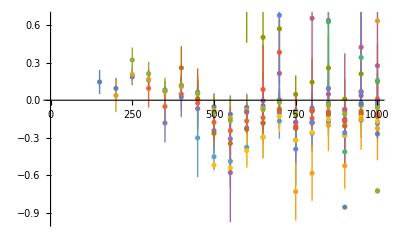

```mathematica
ListPlot[Table[Table[{tRs[[t0,tR]],Around[-eigenVecs[[t0,tR,1,2]],CI[-booteigenVecs[[All,t0,tR,1,2]]]]},{tR,1,Length[eigenVecs[[t0]]]}],{t0,Length[eigenVecs]}],Joined->False]
```

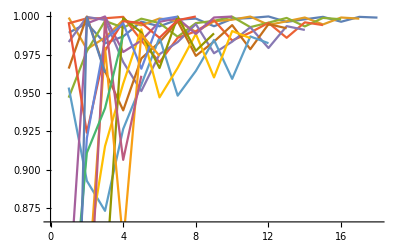

```mathematica
ListPlot[-eigenVecs[[All,All,1,1]],Joined->True]
```

```mathematica
-eigenVecs[[-1,-1,1]]
```

{0.690349,-0.723476}

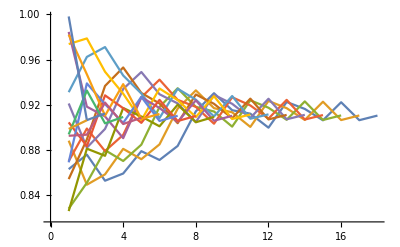

```mathematica
ListPlot[-eigenVecs[[All,All,2,2]],Joined->True]
```

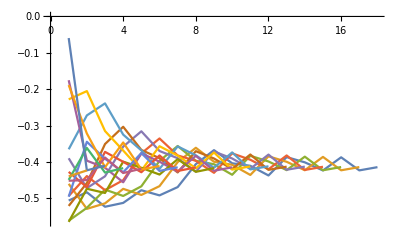

```mathematica
ListPlot[-eigenVecs[[All,All,2,1]],Joined->True]
```

```mathematica
-eigenVecs[[-1,-1,2]]
```

{-0.385309,0.922788}

```mathematica
Total[Total/@evals]
```

171

```mathematica
Dimensions[evals]
```

{19}

```mathematica
Table[
```

```mathematica
evecs
```

{{-0.740865,-0.671654},{0.701492,-0.712677}}

```mathematica
gevpCorrs=Table[Table[Table[Sum[Sum[Conjugate[evecs[[m,MM]]] mat[[t,MM,NN]]evecs[[n,NN]],{MM,1,2}],{NN,1,2}],{t,1,101}],{m,1,2}],{n,1,2}];
```

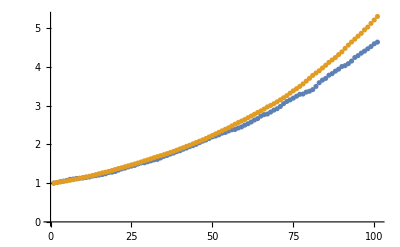

```mathematica
ListPlot[{gevpCorrs[[1,1]]/gevpCorrs[[1,1,1]],gevpCorrs[[2,2]]/gevpCorrs[[2,2,1]]}]
```

```mathematica
EM[tab_]:=Table[1/1Log[tab[[t]]/tab[[t+1]]],{t,Length[tab]-1}]
```

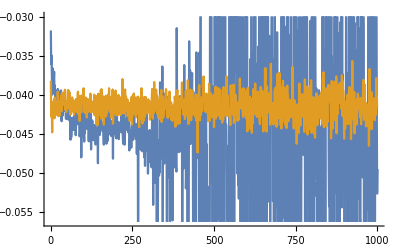

```mathematica
ListPlot[{EM[Table[Mean[WA[[τ]]],{τ,1,1001}]]/.4,EM[Table[Mean[WB[[τ]]],{τ,1,1001}]]/.4},Joined->True]
```

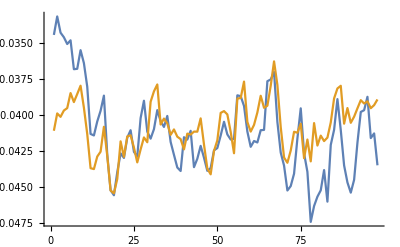

```mathematica
ListPlot[{EM[Table[Mean[WA[[τ]]],{τ,1,101}]]/.4,EM[Table[Mean[WB[[τ]]],{τ,1,101}]]/.4},Joined->True]
```

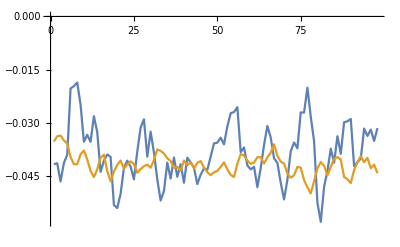

```mathematica
ListPlot[{EM[gevpCorrs[[1,1]]]/.4,EM[gevpCorrs[[2,2]]]/.4},Joined->True]
```

```mathematica
Around[Mean[EM[Table[Mean[WA[[τ]]],{τ,1,101}]]],StandardDeviation[EM[Table[Mean[WA[[τ]]],{τ,1,101}]]]]/.4
```

-0.04130.0029

```mathematica
Around[Mean[EM[Table[Mean[WB[[τ]]],{τ,1,101}]]],StandardDeviation[EM[Table[Mean[WB[[τ]]],{τ,1,101}]]]]/.4
```

-0.04080.0018

```mathematica
Around[Mean[EM[gevpCorrs[[1,1]]]],StandardDeviation[EM[gevpCorrs[[1,1]]]]]/.4
```

-0.04170.0028

```mathematica
Around[Mean[EM[gevpCorrs[[2,2]]]],StandardDeviation[EM[gevpCorrs[[2,2]]]]]/.4
```

-0.0380.009

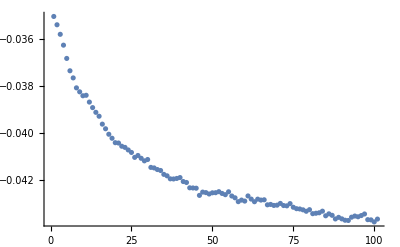

```mathematica
Show[ListPlot[Table[Mean[HamA[[τ]]WA[[τ]]]/Mean[WA[[τ]]],{τ,1,101}]],Plot[Exp[-(-.041)τ .4],{τ,0,101},PlotStyle->ColorData[97][2]]]
```

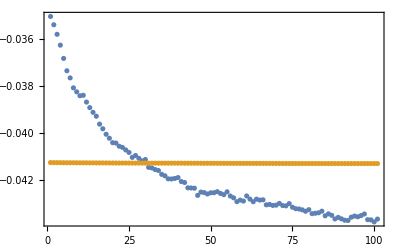

```mathematica
Show[ListPlot[{Table[Mean[HamA[[τ]]WA[[τ]]]/Mean[WA[[τ]]],{τ,1,101}],Table[Mean[HamB[[τ]]WB[[τ]]]/Mean[WB[[τ]]],{τ,1,101}]}],PlotRange->All,Axes->False,Frame->True]
```

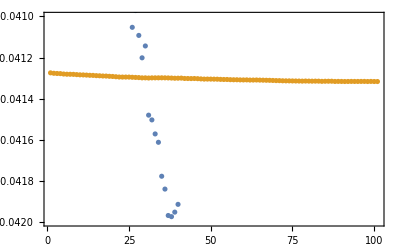

```mathematica
Show[ListPlot[{Table[Mean[HamA[[τ]]WA[[τ]]]/Mean[WA[[τ]]],{τ,1,101}],Table[Mean[HamB[[τ]]WB[[τ]]]/Mean[WB[[τ]]],{τ,1,101}]}],PlotRange->{-.042,-.041},Axes->False,Frame->True]
```

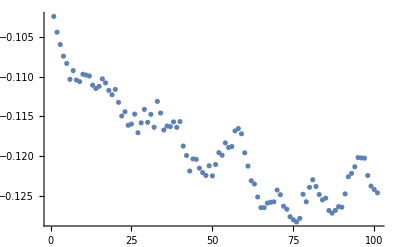

```mathematica
Show[ListPlot[Table[(Mean[HamI1[[τ]]WI1[[τ]]]/Mean[WI1[[τ]]])/Sqrt[Abs[Mean[HamI4[[τ]]WI4[[τ]]]/Mean[WI4[[τ]]]]],{τ,1,101}]],Plot[Exp[-(-.041)τ .4],{τ,0,101},PlotStyle->ColorData[97][2]]]
```

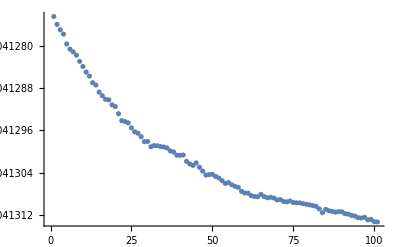

```mathematica
Show[ListPlot[Table[Mean[HamB[[τ]]],{τ,1,101}]],Plot[Exp[-(-.041)τ .4],{τ,0,101},PlotStyle->ColorData[97][2]]]
```

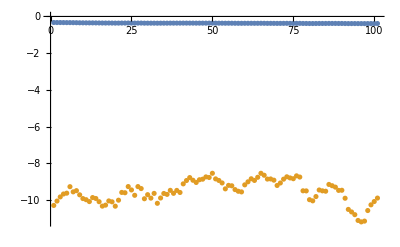

```mathematica
Show[ListPlot[{Table[Mean[HamI1[[τ]]],{τ,1,101}],Table[Mean[HamI4[[τ]]],{τ,1,101}]}],Plot[Exp[-(-.041)τ .4],{τ,0,101},PlotStyle->ColorData[97][2]]]
```

```mathematica
Show[ListPlot[{Table[Mean[HamI1[[τ]]],{τ,1,101}],Table[Mean[HamI4[[τ]]],{τ,1,101}]}],Plot[Exp[-(-.041)τ .4],{τ,0,101},PlotStyle->ColorData[97][2]]]
```

```mathematica
HamI1[[2]]/HamI4[[2]]
```

Null

```mathematica
Table[Eigenvalues[{{{Mean[WA[[τ]]],.22},{.22,Mean[WB[[τ]]]}},{{Mean[WA[[τ+1]]],.22},{.22,Mean[WB[[τ+1]]]}}}],{τ,1,100}]
```

{{0.987528,0.979986},{0.987645,0.980269},{0.988544,0.981787},{0.988706,0.982018},{0.986711,0.97965},{0.98837,0.982225},{0.988331,0.982133},{0.987176,0.980905},{0.986858,0.980608},{0.988452,0.982838},{0.988111,0.982375},{0.985576,0.979036},{0.98665,0.980498},{0.985072,0.978607},{0.985377,0.979149},{0.987508,0.981985},{0.98554,0.979565},{0.986666,0.981345},{0.984194,0.977971},{0.982937,0.976361},{0.986294,0.981159},{0.985378,0.980021},{0.984816,0.979323},{0.985493,0.98035},{0.986739,0.982158},{0.985008,0.979931},{0.984164,0.978913},{0.985991,0.981354},{0.986984,0.982316},{0.985132,0.980466},{0.984674,0.979748},{0.988156,0.984006},{0.98577,0.981544},{0.985446,0.981194},{0.985987,0.981955},{0.985733,0.981645},{0.985645,0.981564},{0.984558,0.980311},{0.985656,0.981147},{0.984794,0.980806},{0.984266,0.980159},{0.986263,0.98254},{0.985262,0.981494},{0.984433,0.980681},{0.985065,0.981006},{0.985441,0.982047},{0.985333,0.981988},{0.983378,0.979588},{0.984002,0.980439},{0.98518,0.981927},{0.98491,0.98149},{0.984389,0.981155},{0.986624,0.983822},{0.985332,0.982388},{0.983775,0.980474},{0.985697,0.982904},{0.984696,0.981347},{0.987667,0.984728},{0.985625,0.982972},{0.984712,0.981902},{0.984846,0.982109},{0.98462,0.981944},{0.985141,0.982526},{0.985441,0.982441},{0.985699,0.983276},{0.984622,0.982098},{0.987538,0.984551},{0.986869,0.983925},{0.985885,0.983472},{0.984215,0.981822},{0.983739,0.981072},{0.984075,0.981706},{0.98325,0.980323},{0.984506,0.981693},{0.985205,0.983158},{0.984466,0.981942},{0.985677,0.983763},{0.982183,0.979651},{0.984542,0.981891},{0.983347,0.980189},{0.984862,0.98144},{0.983772,0.981592},{0.984075,0.980815},{0.984728,0.982801},{0.98294,0.980126},{0.986294,0.984526},{0.986433,0.984327},{0.984091,0.982328},{0.985509,0.98299},{0.983444,0.981293},{0.984852,0.981465},{0.984353,0.982097},{0.984022,0.98228},{0.985798,0.984275},{0.985544,0.98411},{0.983868,0.982309},{0.986345,0.985019},{0.984325,0.981375},{0.984131,0.982688},{0.986134,0.983079}}

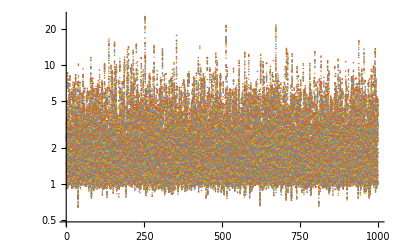

```mathematica
ListLogPlot[WA]
```

```mathematica
meanA=Mean[HamA*WA]/Mean[WA];
```

```mathematica
meanB=Mean[HamB*WB]/Mean[WB];
```

```mathematica
meanC=Mean[HamC*WC]/Mean[WC];
```

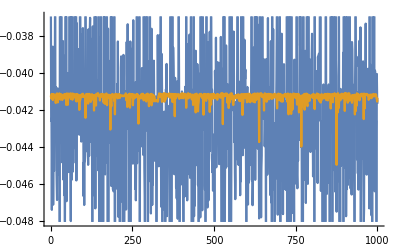

```mathematica
ListPlot[{meanA,meanB},Joined->True]
```

```mathematica
<n|m> = int dx psi_n(x) psi_m(x) = 0
```

```mathematica
for all x, psi_n(x) psi_m(x) >= 0
```

```mathematica
for some x, psi_n(x) psi_m(x) > 0
```

```mathematica
int dx psi_n(x)psi_m(x) > 0
```

```mathematica
I1=int A(x)B(x) / int |A(x)|^2=<B(x)/A(x)>_{prob=|A|^2}
```

```mathematica
I2=int A(x)B(x) / int |B(x)|^2=<A(x)/B(x)>_{prob=|B|^2}
```

```mathematica
I3=int |A(x)|^2 / int |B(x)|^2=<|A(x)/B(x)|^2>_{prob=|B|^2}
```

```mathematica
I4=int |B(x)|^2 / int |A(x)|^2=<|B(x)/A(x)|^2>_{prob=|A|^2}
```

```mathematica
ϵ=int A(x)B(x)/sqrt( int|A|^2 int |B|^2)=I1 Sqrt[I3]=I1/Sqrt[I4]
```

```mathematica
C(τ=0)={{<AA>,<AB>},{<BA>,<BB>}} = {{1,ϵ},{ϵ,1}}
```

```mathematica
C(τ)={{<AA(τ)>,<AB(τ)>},{<BA(τ)>,<BB(τ)>}}
```

```mathematica
C(τ)(C(τ0))^(-1)
```

```mathematica
Eigenvectors[{{1,ϵ},{ϵ,1}}]
```

{{-1,1},{1,1}}

```mathematica
Mean[meanA]
```

-0.0423889

```mathematica
StandardDeviation[meanA]
```

0.00410067

```mathematica
Mean[meanB]
```

-0.0413053

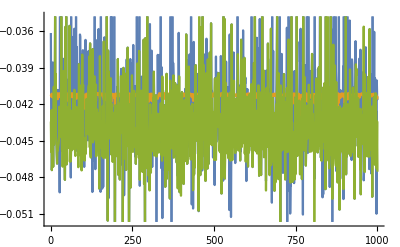

```mathematica
ListPlot[{meanA,meanB,meanC},Joined->True]
```

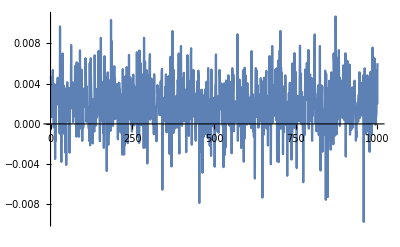

```mathematica
ListPlot[{1/2meanA+1/2meanB-meanC},Joined->True]
```

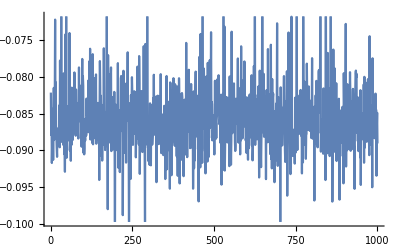

```mathematica
ListPlot[{1/2meanA+1/2meanB+meanC},Joined->True]
```

## Check color states

```mathematica
dE4
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]

colorList={ColorData[97][3],ColorData[97][10],ColorData[97][1],ColorData[97][2]}

Fig2legend=LineLegend[Table[colorList[[ii]],{ii,4}],{MaTeX["1\\otimes 1  {\\phantom{t}} (g=0)",Magnification->0.8],MaTeX["1\\otimes 1 {\\phantom{t}}(g=1)",Magnification->0.8],MaTeX["3\\otimes \\bar 3",Magnification->0.8],MaTeX["6\\otimes \\bar 6",Magnification->0.8]},LegendLayout->{"Column",4},LegendMargins->0.2,LegendFunction->frame]
```

{RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051]}

```mathematica
dropboxDir="~/bassi/heavy_quark_nuclei/"
```

~/bassi/heavy_quark_nuclei/

```mathematica
HamALO=Import[dropboxDir<>"Hammys_LO_dtau0.04_Nstep600_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.75_spoila1.00033_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.82843_masses[1.0, -1.0, 1.0, -1.0]_color_1x1_g0.0.h5",{"Datasets","Hammys"}][[All,All,1]];
HamALO2=Import[dropboxDir<>"Hammys_LO_dtau0.04_Nstep600_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.75_spoila1.00033_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.82843_masses[1.0, -1.0, 1.0, -1.0]_color_1x1_g1.0.h5",{"Datasets","Hammys"}][[All,All,1]];
HamANLO=Import[dropboxDir<>"Hammys_LO_dtau0.04_Nstep600_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.75_spoila2.50066_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac1.5_masses[1.0, 1.0, -1.0, -1.0]_color_3x3bar_g1.0.h5",{"Datasets","Hammys"}][[All,All,1]];
HamANNLO=Import[dropboxDir<>"Hammys_LO_dtau0.04_Nstep600_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.75_spoila6.0_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac0.5_masses[1.0, 1.0, -1.0, -1.0]_color_6x6bar_g1.0.h5",{"Datasets","Hammys"}][[All,All,1]];
```

```mathematica
WALO=Import[dropboxDir<>"Hammys_LO_dtau0.04_Nstep600_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.75_spoila1.00033_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.82843_masses[1.0, -1.0, 1.0, -1.0]_color_1x1_g0.0.h5",{"Datasets","Ws"}][[All,All,1]];
WALO2=Import[dropboxDir<>"Hammys_LO_dtau0.04_Nstep600_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.75_spoila1.00033_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.82843_masses[1.0, -1.0, 1.0, -1.0]_color_1x1_g1.0.h5",{"Datasets","Ws"}][[All,All,1]];
WANLO=Import[dropboxDir<>"Hammys_LO_dtau0.04_Nstep600_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.75_spoila2.50066_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac1.5_masses[1.0, 1.0, -1.0, -1.0]_color_3x3bar_g1.0.h5",{"Datasets","Ws"}][[All,All,1]];
WANNLO=Import[dropboxDir<>"Hammys_LO_dtau0.04_Nstep600_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.75_spoila6.0_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac0.5_masses[1.0, 1.0, -1.0, -1.0]_color_6x6bar_g1.0.h5",{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
Monitor[matHamE1=Table[{BootstrapMeanStdDev[HamALO[[t]],WALO[[t]],50],BootstrapMeanStdDev[HamALO2[[t]],WALO2[[t]],50],BootstrapMeanStdDev[HamANLO[[t]],WANLO[[t]],50],BootstrapMeanStdDev[HamANNLO[[t]],WANNLO[[t]],50]},{t,1,600}],t];
```

```mathematica
BootstrapMeanStdDev[HamANLO[[250]],WANLO[[250]],50]//Timing
```

{0.00265,BootstrapMeanStdDev(Symbol[]⟦250⟧,Symbol[]⟦250⟧,50)}

```mathematica
HamANLO[[250]]
```

Symbol[]⟦250⟧

```mathematica
matHamE1[[All,1]][[100,1]]
```

-0.469276

```mathematica
(*Assuming yData is your list of 500 points like {{centralValue1,error1},{centralValue2,error2},...}*)(*Example:yData=Table[{RandomReal[{0,1}],RandomReal[{0.1,0.2}]},{500}];*)(*Generate taus*)taus=Table[t*0.04,{t,1,600}];

(*Preparing data for plotting*)
dataWithErrorsLO=Table[{taus[[i]],Around[matHamE1[[All,1]][[i,1]],matHamE1[[All,1]][[i,2]]]},{i,1,Length[taus]}];
dataWithErrorsLO2=Table[{taus[[i]],Around[matHamE1[[All,2]][[i,1]],matHamE1[[All,2]][[i,2]]]},{i,1,Length[taus]}];
dataWithErrorsNLO=Table[{taus[[i]],Around[matHamE1[[All,3]][[i,1]],matHamE1[[All,3]][[i,2]]]},{i,1,Length[taus]}];
dataWithErrorsNNLO=Table[{taus[[i]],Around[matHamE1[[All,4]][[i,1]],matHamE1[[All,4]][[i,2]]]},{i,1,Length[taus]}];
```

```mathematica
meanErrorLO1={-0.4794070,0.001393};
(*meanErrorLO2={-0.47551764,0.00871};
meanErrorNLO={-0.407606,0.00565};
meanErrorNNLO={-0.435437,0.0035081};*)

bands={{Opacity[0.3,ColorData[97][3]],Rectangle[{0,meanErrorLO1[[1]]-meanErrorLO1[[2]]},{5800000,meanErrorLO1[[1]]+meanErrorLO1[[2]]}]}(*{Opacity[0.3,ColorData[97][1]],Rectangle[{0,meanErrorNLO[[1]]-meanErrorNLO[[2]]},{5800000,meanErrorNLO[[1]]+meanErrorNLO[[2]]}]},{Opacity[0.3,ColorData[97][2]],Rectangle[{0,meanErrorNNLO[[1]]-meanErrorNNLO[[2]]},{5800000,meanErrorNNLO[[1]]+meanErrorNNLO[[2]]}]}*)};
```

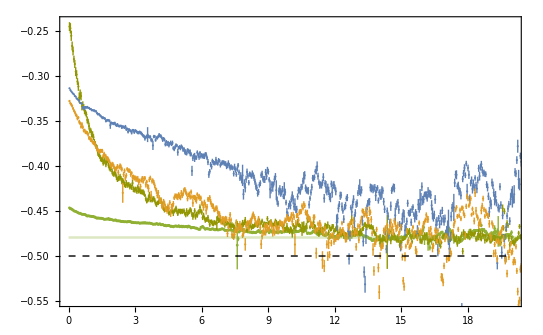

```mathematica
ΔEqqqqPlotmq=Legended[Show[ListPlot[dataWithErrorsLO,PlotRange->{{0,20},{-0.24,-0.55}},PlotStyle->ColorData[97][3]],ListPlot[dataWithErrorsLO2,PlotRange->{{0,20},{-0.24,-0.55}},PlotStyle->ColorData[97][10]],ListPlot[dataWithErrorsNLO,PlotRange->{{0,20},{-0.1,-0.6}},PlotStyle->ColorData[97][1]],ListPlot[dataWithErrorsNNLO,PlotRange->{{0,20},{-0.1,-0.6}},PlotStyle->ColorData[97][2]],Graphics[bands],Graphics[{Dashed,Line[{{0,-0.5},{20,-0.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX[" \\tau m_Q \\alpha^2",Magnification->1.2],MaTeX["\\Delta E_{Q\\bar{Q}Q\\bar{Q}}(\\tau)/m_Q/\\alpha^2",Magnification->1.2]}],Placed[Fig2legend,{0.5,0.9}]]
```

```mathematica
HamALO=Import[dropboxDir<>"Hammys_LO_dtau0.005_Nstep1000_Nwalkers2000_Ncoord4_Nc3_nskip100_Nf4_alpha0.75_spoila1.00033_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.82843_masses[1.0, -20.0, 1.0, -20.0]_color_1x1_g0.0.h5",{"Datasets","Hammys"}][[All,All,1]];
WALO=Import[dropboxDir<>"Hammys_LO_dtau0.005_Nstep1000_Nwalkers2000_Ncoord4_Nc3_nskip100_Nf4_alpha0.75_spoila1.00033_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.82843_masses[1.0, -20.0, 1.0, -20.0]_color_1x1_g0.0.h5",{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
Monitor[matHamE1=Table[{BootstrapMeanStdDev[HamALO[[t]],WALO[[t]],50],BootstrapMeanStdDev[HamANLO[[t]],WANLO[[t]],50],BootstrapMeanStdDev[HamANNLO[[t]],WANNLO[[t]],50]},{t,1,1000}],t];
```

```mathematica
BootstrapMeanStdDev[HamALO[[250]],WALO[[250]],50]//Timing
```

{0.021969,{-1.07854,0.0147788}}

```mathematica
(*Assuming yData is your list of 500 points like {{centralValue1,error1},{centralValue2,error2},...}*)(*Example:yData=Table[{RandomReal[{0,1}],RandomReal[{0.1,0.2}]},{500}];*)(*Generate taus*)taus=Table[t*0.005,{t,1,1000}];

(*Preparing data for plotting*)
dataWithErrorsLO=Table[{taus[[i]],Around[matHamE1[[All,1]][[i,1]],matHamE1[[All,1]][[i,2]]]},{i,1,Length[taus]}];
```

```mathematica
meanErrorLO={-1.428605632634,0.0712304};

bands={{Opacity[0.3,ColorData[97][3]],Rectangle[{0,meanErrorLO[[1]]-meanErrorLO[[2]]},{5800000,meanErrorLO[[1]]+meanErrorLO[[2]]}]},(*{Opacity[0.3,ColorData[97][1]],Rectangle[{0,meanErrorNLO[[1]]-meanErrorNLO[[2]]},{5800000,meanErrorNLO[[1]]+meanErrorNLO[[2]]}]},{Opacity[0.3,ColorData[97][2]],Rectangle[{0,meanErrorNNLO[[1]]-meanErrorNNLO[[2]]},{5800000,meanErrorNNLO[[1]]+meanErrorNNLO[[2]]}]}*)};
```

```mathematica
dataWithErrorsLO[[1]]
```

{0.005,Symbol[]⟦1⟧Symbol[]⟦1⟧}

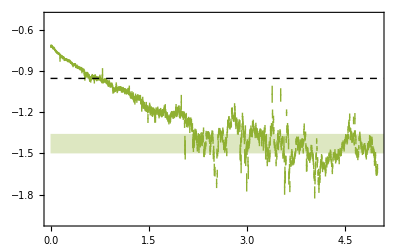

```mathematica
ΔEqqqqPlotmq=Show[ListPlot[dataWithErrorsLO,PlotRange->{{0,5},{-0.50,-2}},PlotStyle->ColorData[97][3]],Graphics[bands],Graphics[{Dashed,Line[{{0,-20/21},{20,-20/21}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX[" \\tau m_Q \\alpha^2",Magnification->1.2],MaTeX["\\Delta E_{Q\\bar{Q}Q\\bar{Q}}(\\tau)/m_Q/\\alpha^2",Magnification->1.2]}]
```

## Uneq mass scan

{{0.4,0},{1/5,0},{1/10,0.0000.015},{1/15,0.2240.020},{1/20,0.430.04},{1/25,0.6990.029},{1/30,0.800.07}}

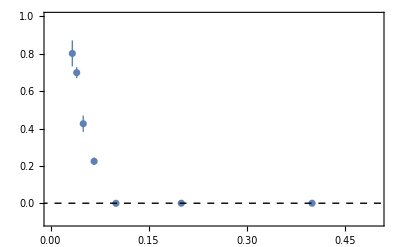

```mathematica
vmcTab={{1/2.5,(*Around[-(2.5/3.5-0.64645390),0.00249351]*)0},{1/5,(*Around[-(5/6-0.761627712684),0.004111100]*) 0},{1/10,Around[-(10/11-0.908735189751),0.0148628]},{1/15,Around[-(15/16-1.161886616999),0.0202457071]},{1/20,Around[-(20/21-1.3780625),0.04324622960]},{1/25,Around[-(25/26-1.660691),0.029470948]},{1/30,Around[-(30/31-1.769787182),0.0694716]}}

Show[ListPlot[vmcTab],Graphics[{Black,Dashed,Line[{{-10,0},{10,0}}]}],Axes->False,Frame->True,PlotRange->{{0,0.5},{-.1,1}}]
```

## GFMC old

```mathematica
matHamE1p=Table[{BootstrapMeanStdDevDifference[HamALO[[t]],WALO[[t]],HamALOp[[t]],WALOp[[t]],100],BootstrapMeanStdDevDifference[HamANLO[[t]],WANLO[[t]],HamANLOp[[t]],WANLOp[[t]],100],BootstrapMeanStdDevDifference[HamANNLO[[t]],WANNLO[[t]],HamANNLOp[[t]],WANNLOp[[t]],100]},{t,1,2000}];
```

```mathematica
(*Assuming yData is your list of 500 points like {{centralValue1,error1},{centralValue2,error2},...}*)(*Example:yData=Table[{RandomReal[{0,1}],RandomReal[{0.1,0.2}]},{500}];*)(*Generate taus*)
taus=Table[t*4800,{t,1,2000}];
(*Preparing data for plotting*)
dataWithErrorsLOp=Table[{taus[[i]],Around[-matHamE1p[[All,1]][[i,1]],matHamE1p[[All,1]][[i,2]]]},{i,1,Length[taus]}];
dataWithErrorsNLOp=Table[{taus[[i]],Around[-matHamE1p[[All,2]][[i,1]],matHamE1p[[All,2]][[i,2]]]},{i,1,Length[taus]}];
dataWithErrorsNNLOp=Table[{taus[[i]],Around[-matHamE1p[[All,3]][[i,1]],matHamE1p[[All,3]][[i,2]]]},{i,1,Length[taus]}];
```

```mathematica
BEqqqqPlotmq=Legended[Legended[Show[ListPlot[dataWithErrorsLOp,PlotRange->{{0,5800000},{0,6.8 10^-8}},PlotStyle->ColorData[97][1]],ListPlot[dataWithErrorsNLOp,PlotRange->{{0,5800000},{0,6.8 10^-8}},PlotStyle->ColorData[97][2]],ListPlot[dataWithErrorsNNLOp,PlotRange->{{0,5800000},{0,6.8 10^-8}},PlotStyle->ColorData[9][2]],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX[" \\tau m_Q",Magnification->1.2],MaTeX["B_{Q\\bar{Q}Q\\bar{Q}}(\\tau)/m_Q",Magnification->1.2]}],Placed[Fig2legend,{0.5,0.12}]],Placed[MaTeX["\\alpha_s=10^{-3}"],{0.87,0.91}]]
```

-Graphics-

```mathematica
HamALO=Around[Import[dropboxDir<>"Hammys_LO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac10.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]]];
HamANLO=Import[dropboxDir<>"Hammys_NLO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac10.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]];
HamANNLO=Import[dropboxDir<>"Hammys_NNLO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac10.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]];
HamALOp=Import[dropboxDir<>"Hammys_LO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_product_afac100000000.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]];
HamANLOp=Import[dropboxDir<>"Hammys_NLO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_product_afac100000000.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]];
HamANNLOp=Import[dropboxDir<>"Hammys_NNLO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_product_afac100000000.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]];
```

```mathematica
WALO=Import[dropboxDir<>"Hammys_LO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac10.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]];
WANLO=Import[dropboxDir<>"Hammys_NLO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac10.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]];
WANNLO=Import[dropboxDir<>"Hammys_NNLO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac10.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]];
WALOp=Import[dropboxDir<>"Hammys_LO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_product_afac100000000.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]];
WANLOp=Import[dropboxDir<>"Hammys_NLO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_product_afac100000000.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]];
WANNLOp=Import[dropboxDir<>"Hammys_NNLO_dtau0.4_Nstep2000_Nwalkers2001_Ncoord4_Nc3_nskip100_Nf4_alpha0.1_spoila1_spoilaket1_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_product_afac100000000.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
WANLO//Length
```

501

```mathematica
matHamE1=Table[{BootstrapMeanStdDev[HamALO[[1,t]],WALO[[t]],100],BootstrapMeanStdDev[HamANLO[[t]],WANLO[[t]],100],BootstrapMeanStdDev[HamANNLO[[t]],WANNLO[[t]],100]},{t,1,500}];
```

```mathematica
taus=Table[t*0.4,{t,1,500}];
```

```mathematica
matHamE1[[All,1]][[1,2]]
```

8.68851×10^-12

```mathematica
matHamE1[[All,3]][[1,1]]
```

-0.0157423

```mathematica
(*Assuming yData is your list of 500 points like {{centralValue1,error1},{centralValue2,error2},...}*)(*Example:yData=Table[{RandomReal[{0,1}],RandomReal[{0.1,0.2}]},{500}];*)(*Generate taus*)taus=Table[t*0.4,{t,1,500}];

(*Preparing data for plotting*)
dataWithErrorsLO=Table[{taus[[i]],Around[matHamE1[[All,1]][[i,1]],matHamE1[[All,1]][[i,2]]]},{i,1,Length[taus]}];
dataWithErrorsNLO=Table[{taus[[i]],Around[matHamE1[[All,2]][[i,1]],matHamE1[[All,2]][[i,2]]]},{i,1,Length[taus]}];
dataWithErrorsNNLO=Table[{taus[[i]],Around[matHamE1[[All,3]][[i,1]],matHamE1[[All,3]][[i,2]]]},{i,1,Length[taus]}];
```

```mathematica
ΔEqqqqPlotmq=Legended[Legended[Show[ListPlot[dataWithErrorsLO,PlotRange->{{0,200},{-20*10^-3,-6*10^-3}},PlotStyle->ColorData[97][1]],ListPlot[dataWithErrorsNLO,PlotRange->{{0,200},{-20*10^-3,-6*10^-3}},PlotStyle->ColorData[97][2]],ListPlot[dataWithErrorsNNLO,PlotRange->{{0,200},{-20*10^-3,-6*10^-3}},PlotStyle->ColorData[9][2]],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX[" \\tau m_Q",Magnification->1.2],MaTeX["\\Delta E_{Q\\bar{Q}Q\\bar{Q}}(\\tau)/m_Q",Magnification->1.2]}],Placed[Fig2legend,{0.5,0.12}]],Placed[MaTeX["\\alpha_s=0.1"],{0.9,0.93}]]
```

-Graphics-

-Graphics-

```mathematica
matHamE1p=Table[{BootstrapMeanStdDevDifference[HamALO[[1,t]],WALO[[t]],HamALOp[[t]],WALOp[[t]],100],BootstrapMeanStdDevDifference[HamANLO[[t]],WANLO[[t]],HamANLOp[[t]],WANLOp[[t]],100],BootstrapMeanStdDevDifference[HamANNLO[[t]],WANNLO[[t]],HamANNLOp[[t]],WANNLOp[[t]],100]},{t,1,500}];
```

```mathematica
(*Assuming yData is your list of 500 points like {{centralValue1,error1},{centralValue2,error2},...}*)(*Example:yData=Table[{RandomReal[{0,1}],RandomReal[{0.1,0.2}]},{500}];*)(*Generate taus*)taus=Table[t*0.4,{t,1,500}];

(*Preparing data for plotting*)
dataWithErrorsLOp=Table[{taus[[i]],Around[-matHamE1p[[All,1]][[i,1]],matHamE1p[[All,1]][[i,2]]]},{i,1,Length[taus]}];
dataWithErrorsNLOp=Table[{taus[[i]],Around[-matHamE1p[[All,2]][[i,1]],matHamE1p[[All,2]][[i,2]]]},{i,1,Length[taus]}];
dataWithErrorsNNLOp=Table[{taus[[i]],Around[-matHamE1p[[All,3]][[i,1]],matHamE1p[[All,3]][[i,2]]]},{i,1,Length[taus]}];
```

```mathematica
dataWithErrorsNLOp[[1]]
```

{0.4,0.000450.00004}

```mathematica
BEqqqqPlotmq=Legended[Legended[Show[ListPlot[dataWithErrorsLOp,PlotRange->{{0,200},{-0.0005,0.0017}},PlotStyle->ColorData[97][1]],ListPlot[dataWithErrorsNLOp,PlotRange->{{0,200},{-0.0005,0.0017}},PlotStyle->ColorData[97][2]],ListPlot[dataWithErrorsNNLOp,PlotRange->{{0,200},{-0.0005,0.0017}},PlotStyle->ColorData[9][2]],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX[" \\tau m_Q",Magnification->1.2],MaTeX["B_{Q\\bar{Q}Q\\bar{Q}}(\\tau)/m_Q",Magnification->1.2]}],Placed[Fig2legend,{0.5,0.12}]],Placed[MaTeX["\\alpha_s=0.1"],{0.87,0.91}]]
```

-Graphics-

-Graphics-

```mathematica
HamI1=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket20.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_I1.h5",{"Datasets","Hammys"}][[All,All,1]]
```

{{-0.0388288,-0.0378796,-0.039256,-0.0326763,-0.0312383,-0.0371432,-0.0328664,-0.03891,-0.0427955,-0.0343446,-0.041261,-0.0352431,-0.0375306,-0.0311602,9972,-0.0352492,-0.0445102,-0.0389954,-0.0349016,-0.0363893,-0.0380582,0.010713,-0.0466088,-0.0335564,-0.0312258,-0.0465905,-0.0161461,-0.0075631,-0.0438229},999,{1}}
 |  |  |  |

```mathematica
WI1=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket20.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_I1.h5",{"Datasets","Ws"}][[All,All,1]]
```

{{4.20555,7.27746,10.3117,6.26366,3.89611,6.39446,2.16444,6.90196,11.2051,3.50358,3.89114,4.20782,5.28951,3.49192,6.12441,3.72277,9968,3.48901,27.7533,5.17294,6.29094,8.4774,4.4433,4.66776,6.32563,1.44424,6.2758,4.54782,4.05183,3.58733,1.90593,1.71628,6.04006},999,{1}}
 |  |  |  |

```mathematica
HamI4=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket20.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_I4.h5",{"Datasets","Hammys"}][[All,All,1]]
```

{{-0.0388288,-0.0378796,-0.039256,-0.0326763,-0.0312383,-0.0371432,-0.0328664,-0.03891,-0.0427955,-0.0343446,-0.041261,-0.0352431,-0.0375306,-0.0311602,9972,-0.0352492,-0.0445102,-0.0389954,-0.0349016,-0.0363893,-0.0380582,0.010713,-0.0466088,-0.0335564,-0.0312258,-0.0465905,-0.0161461,-0.0075631,-0.0438229},999,{1}}
 |  |  |  |

```mathematica
WI4=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket20.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_I4.h5",{"Datasets","Ws"}][[All,All,1]]
```

{{17.6867,52.9614,106.331,39.2335,15.1796,40.8891,4.68479,47.637,125.555,12.2751,15.1409,17.7057,27.9789,12.1935,37.5084,13.859,9968,12.1732,770.243,26.7593,39.5759,71.8664,19.7429,21.788,40.0136,2.08581,39.3856,20.6827,16.4174,12.8689,3.63255,2.94561,36.4824},999,{1}}
 |  |  |  |

```mathematica
WI4[[1]]
```

```mathematica
HamI1[[1]]/HamA[[1]]
```

```mathematica
Dimensions[WA]
```

{1001,10000}

```mathematica
Show[ListLogPlot[Table[Mean[WA[[τ]]],{τ,1,1001}]],LogPlot[Exp[-(-.045)τ .4],{τ,0,1001},PlotStyle->ColorData[97][2]]]
```

-Graphics-

```mathematica
Show[ListLogPlot[Table[Mean[WB[[τ]]],{τ,1,1001}]],LogPlot[Exp[-(-.042)τ .4],{τ,0,1001},PlotStyle->ColorData[97][2]]]
```

-Graphics-

```mathematica
fac=Mean[WI1[[1]]]/Sqrt[Mean[WI4[[1]]]]
```

0.426966

```mathematica
Show[ListLogPlot[Table[Mean[WI1[[τ]]]/Sqrt[Mean[WI4[[1]]]],{τ,1,1001}]],LogPlot[fac Exp[-(-.045)τ .4],{τ,0,1001},PlotStyle->ColorData[97][2]]]
```

-Graphics-

```mathematica
mat=Table[{{Mean[WA[[τ]]],Mean[WI1[[τ]]]/Sqrt[Mean[WI4[[1]]]]},{Mean[WI1[[τ]]]/Sqrt[Mean[WI4[[1]]]],Mean[WB[[τ]]]}},{τ,1,1001}];
```

```mathematica
mat=Table[{{Mean[WA[[τ]]],Mean[WI1[[τ]]]/Sqrt[Mean[WI4[[τ]]]]},{Mean[WI1[[τ]]]/Sqrt[Mean[WI4[[τ]]]],Mean[WB[[τ]]]}},{τ,1,1001}];
```

```mathematica
matHam=Table[{{Mean[WA[[τ]]HamA[[τ]]]/Mean[WA[[τ]]],Mean[HamI1[[τ]]WI1[[τ]]]/Mean[WI1[[τ]]]},{Mean[HamI1[[τ]]WI1[[τ]]]/Mean[WI1[[τ]]],Mean[WB[[τ]]HamB[[τ]]]/Mean[WB[[τ]]]}},{τ,1,1001}];
```

```mathematica
ListPlot[{matHam[[All,1,1]],matHam[[All,1,2]],matHam[[All,2,2]]},Frame->True]
```

-Graphics-

```mathematica
NMeas=Length[WA[[1]]]
```

10000

```mathematica
NBoot=200;
```

```mathematica
bootIndices=RandomInteger[{1,NMeas},{NBoot,NMeas}];
```

```mathematica
Dimensions[bootIndices]
```

{200,10000}

```mathematica
bootmat=ParallelTable[Print[b];Table[{{Mean[WA[[τ,bootIndices[[b]]]]],
Mean[WI1[[τ,bootIndices[[b]]]]]/Sqrt[Mean[WI4[[τ,bootIndices[[b]]]]]]},{Mean[WI1[[τ,bootIndices[[b]]]]]/Sqrt[Mean[WI4[[τ,bootIndices[[b]]]]]],
Mean[WB[[τ,bootIndices[[b]]]]]}},{τ,1,1001}],{b,1,NBoot}];
```

1

10

19

28

37

46

2

47

11

20

38

29

3

48

12

21

30

39

4

49

22

40

31

13

5

50

23

32

41

14

24

33

51

42

6

15

25

34

52

7

43

16

26

35

53

44

8

17

27

36

Null

Null

Null

«135 more identical outputs»

198

159

175

183

191

168

199

160

176

184

200

192

```mathematica
ListPlot[bootmat[[1,All,1]]]
```

-Graphics-

```mathematica
t0=100;tref=220;
```

```mathematica
Timing[{evals,evecs}=Eigensystem[{mat[[tref]],mat[[t0]]}]]
```

{0.010264,{{8.94502,6.95328},{{-0.848818,0.528685},{-0.443305,-0.896371}}}}

```mathematica
{evals,evecs}=Eigensystem[{mat[[tref]],mat[[t0]]}]
```

{{8.94502,6.95328},{{-0.848818,0.528685},{-0.443305,-0.896371}}}

```mathematica
{evals,evecs}=Eigensystem[{mat[[tref]],mat[[t0]]}]
```

{{8.94502,6.95328},{{-0.848818,0.528685},{-0.443305,-0.896371}}}

```mathematica
t0s=Table[Table[t0,{tref,t0+50,1000,50}],{t0,100,950,50}];
```

```mathematica
tRs=Table[Table[tref,{tref,t0+50,1000,50}],{t0,100,950,50}];
```

```mathematica
eigenSys=Table[Table[Eigensystem[{mat[[tref]],mat[[t0]]}],{tref,t0+50,1000,50}],{t0,100,950,50}];
```

```mathematica
booteigenSys=ParallelTable[Table[Table[Eigensystem[{bootmat[[b,tref]],bootmat[[b,t0]]}],{tref,t0+50,1000,50}],{t0,100,950,50}],{b,1,NBoot}];
```

```mathematica
eigenVecs=eigenSys[[All,All,2]];
```

```mathematica
eigenVals=eigenSys[[All,All,1]];
```

```mathematica
booteigenVecs=booteigenSys[[All,All,All,2]];
```

```mathematica
UQ=(1+Erf[1/Sqrt[2.]])/2;
LQ=(1-Erf[1/Sqrt[2.]])/2;
```

```mathematica
CI[boots_]:=Block[{LQ,UQ,upper,lower},
UQ=(1+Erf[1/Sqrt[2.]])/2;
LQ=(1-Erf[1/Sqrt[2.]])/2;
upper=Quantile[boots,UQ];
lower=Quantile[boots,LQ];
(upper-lower)/2];
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

Null

Null

Null

«146 more identical outputs»

136

128

152

153

161

169

177

185

193

154

162

170

163

178

186

194

155

171

164

179

172

187

195

156

165

180

188

173

196

157

166

181

189

174

197

158

167

198

190

175

182

168

159

191

176

199

183

Null

Null

Null

«1 more identical outputs»

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

-Graphics-

```mathematica
eigen3pt=Table[Table[(cMat.matHam3pt[[τ]].Transpose[cMat])[[n,n]],{τ,1,Length[mat]}],{n,2}];
```

```mathematica
eigen2pt=Table[Table[(cMat.mat[[τ]].Transpose[cMat])[[n,n]],{τ,1,Length[mat]}],{n,2}];
```

```mathematica
ListLogPlot[{eigen3pt[[1]],eigen2pt[[1]],eigen3pt[[2]],eigen2pt[[2]]}]
```

-Graphics-

```mathematica
ListLogPlot[{eigen2pt[[1]]/mat[[All,1,1]]}]
```

-Graphics-

```mathematica
ListLogPlot[{eigen2pt[[2]]/mat[[All,2,2]]}]
```

-Graphics-

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

-Graphics-

```mathematica
ListPlot[{eigen3pt[[2]]/eigen2pt[[2]],matHam3pt[[All,2,2]]/(mat[[All,2,2]])},Frame->True,PlotRange->{-.05,-.035}]
```

-Graphics-

```mathematica
thresh=-(0.21485 4/3)^2/2
```

-0.0410316

```mathematica
Show[ListPlot[{eigen3pt[[2]]/eigen2pt[[2]],matHam3pt[[All,2,2]]/(mat[[All,2,2]])},Frame->True,PlotRange->{-.044,-.04}],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}]]
```

-Graphics-

```mathematica
eigenHam=Table[eigen3pt[[n]]/eigen2pt[[n]],{n,2}];
```

```mathematica
Show[ListPlot[{matHam[[All,1,1]],matHam[[All,2,2]]},Frame->True],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}],PlotRange->{{1,1000},{-.0455,-.04}}]
```

-Graphics-

```mathematica
Show[ListPlot[{eigenHam[[1]],eigenHam[[2]]},Frame->True],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}],PlotRange->{{1,1000},{-.0455,-.04}}]
```

-Graphics-

```mathematica
stop={500,1001};
```

```mathematica
matHamEM=Table[Table[{(τ-1).4,Around[matHam3pt[[τ,n,n]]/mat[[τ,n,n]],CI[bootmatHam3pt[[All,τ,n,n]]/bootmat[[All,τ,n,n]]]]},{τ,stop[[n]]}],{n,2}];
```

```mathematica
boott0I=RandomInteger[{1,10},NBoot]
```

{6,2,1,8,2,6,4,2,9,2,5,6,3,3,6,2,7,5,10,2,10,6,4,3,9,4,10,6,9,7,3,10,5,10,8,7,1,2,4,4,9,6,1,7,10,4,1,7,9,2,9,1,5,2,4,3,2,5,10,8,9,7,4,8,10,4,2,8,2,5,2,6,5,2,3,10,7,9,9,9,5,7,7,5,3,5,3,1,10,10,4,7,4,4,6,5,3,2,2,1,6,9,6,5,4,3,8,2,4,5,8,5,7,5,2,10,10,3,6,9,9,7,7,6,8,4,6,10,4,4,9,6,8,3,5,1,3,8,4,10,3,5,7,5,2,3,9,6,2,8,1,8,6,2,6,5,1,3,9,10,7,2,2,5,7,9,5,2,5,7,10,3,2,1,8,9,1,5,3,3,10,8,3,4,4,8,3,3,7,5,3,1,5,8,7,7,3,7,10,1}

```mathematica
boottRI=Table[RandomInteger[{1,Length[booteigenVecs[[1,boott0I[[b]]]]]}],{b,NBoot}]
```

{1,16,7,1,1,11,6,15,5,7,13,13,15,6,11,12,8,1,3,7,5,2,11,9,10,9,9,7,2,4,5,4,12,4,1,4,4,5,4,14,2,13,8,10,1,11,4,3,6,5,10,12,14,6,2,4,5,4,2,9,8,11,2,9,2,12,6,3,10,6,12,7,10,6,12,3,11,2,2,2,6,7,5,13,10,1,16,2,3,7,14,7,9,4,9,6,13,3,16,8,12,6,3,11,12,2,11,15,10,13,9,9,9,9,11,2,3,15,12,5,10,6,11,6,4,8,5,8,12,14,6,9,7,8,13,8,6,10,13,9,6,13,8,7,2,14,9,1,12,10,17,3,13,1,1,13,4,5,2,7,5,7,14,8,1,5,3,17,14,1,9,10,5,3,11,8,15,2,10,14,4,9,16,10,5,11,14,12,4,4,2,16,14,8,5,2,12,2,2,1}

```mathematica
-Re[Table[booteigenVecs[[b,boott0I[[b]],boottRI[[b]],1,1]],{b,2}]]
```

{0.992093,0.995004}

```mathematica
Dimensions[booteigenVecs]
```

{200,18}

```mathematica
Dimensions[booteigenVecs[[All,3]]]
```

{200,16,2,2}

```mathematica
bootc11=-Re[Table[booteigenVecs[[b,boott0I[[b]],boottRI[[b]],1,1]],{b,NBoot}]];
```

```mathematica
bootc12=-Re[Table[booteigenVecs[[b,boott0I[[b]],boottRI[[b]],1,2]],{b,NBoot}]];
```

```mathematica
bootc21=-Re[Table[booteigenVecs[[b,boott0I[[b]],boottRI[[b]],2,1]],{b,NBoot}]];
```

```mathematica
bootc22=-Re[Table[booteigenVecs[[b,boott0I[[b]],boottRI[[b]],2,2]],{b,NBoot}]];
```

```mathematica
bootcMat=Table[{{bootc11[[b]],bootc12[[b]]},{bootc21[[b]],bootc22[[b]]}},{b,NBoot}];
```

```mathematica
booteigen3pt=Table[Table[Table[(cMat.bootmatHam3pt[[b,τ]].Transpose[cMat])[[n,n]],{τ,1,Length[mat]}],{n,2}],{b,NBoot}];
```

```mathematica
booteigen2pt=Table[Table[Table[(cMat.bootmat[[b,τ]].Transpose[cMat])[[n,n]],{τ,1,Length[mat]}],{n,2}],{b,NBoot}];
```

```mathematica
booteigen3pt=Table[Table[Table[(bootcMat[[b]].bootmatHam3pt[[b,τ]].Transpose[bootcMat[[b]]])[[n,n]],{τ,1,Length[mat]}],{n,2}],{b,NBoot}];
```

```mathematica
booteigen2pt=Table[Table[Table[(bootcMat[[b]].bootmat[[b,τ]].Transpose[bootcMat[[b]]])[[n,n]],{τ,1,Length[mat]}],{n,2}],{b,NBoot}];
```

```mathematica
booteigenHam=Table[Table[booteigen3pt[[b,n]]/booteigen2pt[[b,n]],{n,2}],{b,NBoot}];
```

```mathematica
eigenHamEM=Table[Table[{(τ-1).4,Around[eigenHam[[n,τ]],CI[booteigenHam[[All,n,τ]]]]},{τ,stop[[n]]}],{n,2}];
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
<<MaTeX`
```

```mathematica
TrimBleed[p2_]:=Show[p2,With[{d=.2},Graphics[{White,FilledCurve[{{Line[ImageScaled/@{{-d,-d},{-d,1+d},{1+d,1+d},{1+d,-d}}]},{Line[Scaled/@{{0,0},{0,1},{1,1},{1,0}}]}}]}]],ImagePadding->{{70,10},{45,10}}]
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
origlegend=PointLegend[Table[Directive[ColorData[97][ii]],{ii,2}],{MaTeX["b/a=5",Magnification->0.8],MaTeX["b/a=100",Magnification->0.8]},LegendMarkers->Table[Automatic,{ii,2}],LegendLayout->{"Column",4},LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
EMPorig=TrimBleed[Show[ListPlot[matHamEM,Joined->False,Frame->True,PlotLegends->Placed[origlegend,{.75,.2}]],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}],PlotRange->{{1,1000 .4},{-.05,-.04}},BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],Frame->True,Axes->False,GridLines->{{0},{0}},FrameLabel->{MaTeX["\\tau \\ m_Q",Magnification->1.2],MaTeX["\\left<\\Psi_T|H(\\tau)|\\Psi_T \\right> / m_Q",Magnification->1.2]}]]
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

-Graphics-

```mathematica
Export[dropboxDir<>"/physics/projects/heavy_quark_nuclei/EMGEVP.pdf",EMPGEVP]
```

~/Dropbox//physics/projects/heavy_quark_nuclei/EMGEVP.pdf

```mathematica
GEVPlegend=PointLegend[Table[Directive[ColorData[97][ii+2]],{ii,2}],{MaTeX["n=0",Magnification->0.8],MaTeX["n=1",Magnification->0.8]},LegendMarkers->Table[Automatic,{ii,2}],LegendLayout->{"Column",4},LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
EMboth=Show[ListPlot[eigenHamEM,Joined->False,Frame->True,PlotLegends->Placed[GEVPlegend,{.725,.2}],PlotStyle->{ColorData[97][3],ColorData[97][4]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][4]}],ListPlot[matHamEM,Joined->False,Frame->True,PlotLegends->Placed[origlegend,{.77,.3}]],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}],PlotRange->{{1,1000 .4},{-.049,-.0405}},BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],Frame->True,Axes->False,GridLines->{{0},{0}},FrameLabel->{MaTeX["\\tau \\ m_Q",Magnification->1.2],MaTeX["\\Delta E_n(\\tau) / m_Q",Magnification->1.2]}]
```

-Graphics-

```mathematica
Export[dropboxDir<>"/physics/projects/heavy_quark_nuclei/EMboth.pdf",EMboth]
```

~/Dropbox//physics/projects/heavy_quark_nuclei/EMboth.pdf

```mathematica
eigenHamEM[[1,250]]
```

{99.6,-0.044530.00019}

```mathematica
eigenHamEM[[2,250]]
```

{99.6,-0.041380.00005}

```mathematica
eigenHamEM[[1,250,2]]-thresh
```

-0.003500.00019

```mathematica
eigenHamEM[[2,250,2]]-thresh
```

-0.000350.00005

```mathematica
mb=4.77050;
```

```mathematica
Mean[(eigenHamEM[[1,200;;350,2]]-thresh)]mb 1000
```

-20.40.6

```mathematica
0.281402*4
```

1.12561

```mathematica
.214850^2(4/3)^2/4/4
```

0.00512895

```mathematica
(eigenHamEM[[2,250;;,2]]-thresh)mb 1000
```

{-1.650.24,-1.650.23,-1.650.23,-1.640.22,-1.640.22,-1.630.22,-1.640.23,-1.630.24,-1.630.24,-1.630.23,-1.630.23,-1.630.22,-1.630.22,-1.640.22,-1.630.21,-1.630.21,-1.630.22,-1.630.22,-1.620.22,-1.630.22,-1.630.22,-1.610.22,-1.610.21,-1.620.21,-1.630.23,-1.620.22,-1.620.21,-1.620.21,-1.620.22,-1.620.21,-1.620.21,-1.630.21,-1.620.20,-1.620.21,-1.630.21,-1.690.23,-1.670.22,-1.800.31,-1.660.22,-1.720.26,-1.660.21,-1.660.21,-1.650.21,-1.640.20,-1.640.21,-1.670.22,-1.640.21,-1.660.22,-1.680.23,-1.740.26,-2.00.5,-1.670.21,-1.700.22,-1.670.21,-1.680.22,-1.710.23,-1.650.21,-1.640.20,-1.660.20,-1.690.22,-1.680.21,-1.780.27,-1.740.24,-1.820.31,-1.760.25,-1.840.32,-1.690.21,-1.720.24,-1.740.24,-1.740.24,-1.750.23,-1.710.21,-1.710.21,-1.700.22,-1.680.22,-1.670.22,-1.680.23,-1.700.23,-1.700.23,-1.690.23,-1.700.22,-1.730.23,-1.740.24,-1.720.22,-1.750.24,-1.730.23,-1.740.24,-1.740.24,-1.730.23,-1.760.25,-1.720.23,-1.710.23,-1.710.22,-1.700.22,-1.710.21,-1.690.22,-1.690.23,-1.730.23,-1.710.22,-1.770.23,-1.740.23,-1.830.28,-1.760.23,-1.770.23,-1.740.22,-1.720.22,-1.720.22,-1.730.23,-1.710.22,-1.740.22,-1.730.22,-1.720.22,-1.740.22,-1.750.22,-1.730.21,-1.720.22,-1.750.23,-1.780.24,-1.790.24,-1.780.24,-1.780.24,-1.790.25,-1.770.25,-1.750.24,-1.750.24,-1.760.24,-1.760.24,-1.760.24,-1.750.22,-1.740.23,-1.740.23,-1.740.22,-1.750.22,-1.720.23,-1.710.23,-1.720.22,-1.710.23,-1.690.21,-1.700.21,-1.720.23,-1.720.23,-1.710.22,-1.710.23,-1.710.23,-1.700.22,-1.710.23,-1.700.23,-1.690.22,-1.690.22,-1.690.21,-1.690.22,-1.690.22,-1.680.22,-1.680.22,-1.700.23,-1.700.23,-1.700.23,-1.710.22,-1.700.22,-1.710.23,-1.730.23,-1.740.22,-1.730.22,-1.740.23,-1.720.22,-1.720.22,-1.730.22,-1.710.22,-1.740.22,-1.760.21,-1.770.22,-1.770.23,-1.780.24,-1.780.23,-1.790.24,-1.720.21,-1.730.21,-1.720.21,-1.730.22,-1.740.22,-1.770.24,-1.750.23,-1.730.23,-1.750.23,-1.740.23,-1.760.23,-1.760.23,-1.790.24,-1.750.23,-1.770.24,-1.810.25,-1.800.25,-1.760.23,-1.770.24,-1.730.23,-1.730.23,-1.700.20,-1.710.21,-1.750.24,-1.760.25,-1.760.24,-1.820.27,-1.860.30,-1.830.28,-1.770.25,-1.740.22,-1.740.23,-1.740.22,-1.740.23,-1.800.25,-2.20.6,-2.10.5,-1.860.30,-1.800.24,-1.780.25,-1.760.24,-1.750.22,-1.740.22,-1.740.22,-1.740.22,-1.790.24,-1.820.24,-1.790.24,-1.820.25,-1.800.23,-1.840.25,-1.840.26,-1.810.24,-1.980.33,-1.890.30,-1.900.30,-1.880.29,-2.00.4,-2.81.3,-2.20.5,-2.10.5,-2.00.4,-1.940.32,-2.10.4,-2.10.5,-3.21.7,-1.980.34,-1.970.31,-1.800.24,-1.770.23,-1.750.21,-1.740.20,-1.810.24,-1.790.22,-1.780.23,-1.780.23,-1.810.24,-1.850.26,-1.750.21,-1.660.19,-1.630.20,-1.680.19,-1.660.21,-1.660.19,-1.710.21,-1.700.20,-1.700.21,-1.680.20,-1.540.23,-1.20.6,-1.10.7,-1.590.21,-1.710.21,-1.630.20,-1.550.24,-1.700.20,-1.710.20,-1.690.20,-1.680.20,-1.690.21,-1.610.20,-1.440.29,-1.40.4,-1.40.4,-1.30.4,-1.540.22,-1.520.24,-1.490.25,-1.490.26,-1.550.21,-1.400.32,-1.620.19,-1.590.20,-1.630.19,-1.700.21,-1.680.21,-1.690.22,-1.680.21,-1.720.22,-1.740.21,-1.740.22,-1.750.22,-1.740.21,-1.760.23,-1.720.21,-1.820.27,-1.890.31,-1.890.33,-1.850.31,-1.850.30,-1.830.28,-1.850.31,-1.850.31,-1.90.4,-1.880.32,-1.860.32,-1.820.28,-1.830.28,-1.770.25,-1.760.25,-1.690.22,-1.700.22,-1.720.24,-1.770.26,-1.770.26,-1.780.26,-1.750.25,-1.780.27,-1.790.27,-1.810.28,-1.800.28,-1.800.28,-1.780.27,-1.770.26,-1.760.25,-1.750.25,-1.770.26,-1.820.29,-1.830.29,-1.840.30,-1.850.31,-1.840.30,-1.840.29,-1.830.29,-1.830.29,-1.840.30,-1.820.28,-1.810.27,-1.820.28,-1.830.28,-1.840.29,-1.810.27,-1.810.28,-1.780.27,-1.740.25,-1.760.25,-1.780.26,-1.720.23,-1.760.25,-1.760.26,-1.780.26,-1.730.23,-1.730.23,-1.740.24,-1.750.25,-1.760.26,-1.740.25,-1.790.27,-1.750.25,-1.770.26,-1.760.25,-1.760.25,-1.750.25,-1.760.25,-1.750.24,-1.700.21,-1.700.21,-1.680.21,-1.670.21,-1.660.22,-1.630.23,-1.580.25,-1.770.26,-1.770.26,-1.720.23,-1.750.24,-1.740.23,-1.690.22,-1.650.22,-1.640.21,-1.640.20,-1.570.25,-1.610.22,-1.580.24,-1.600.23,-1.590.24,-1.600.23,-1.630.22,-1.650.22,-1.670.24,-1.700.23,-1.690.22,-1.650.25,-1.700.24,-1.720.24,-1.750.25,-1.730.25,-1.700.24,-1.740.27,-1.730.26,-1.770.26,-1.760.26,-1.760.27,-1.750.26,-1.740.26,-1.770.28,-1.750.26,-1.730.26,-1.710.25,-1.700.25,-1.670.25,-1.720.25,-1.670.26,-1.690.23,-1.720.24,-1.750.26,-1.720.24,-1.710.24,-1.720.24,-1.680.22,-1.730.24,-1.710.23,-1.720.24,-1.760.26,-1.740.24,-1.760.26,-1.780.27,-1.760.25,-1.750.25,-1.730.23,-1.720.24,-1.730.24,-1.750.25,-1.750.26,-1.750.26,-1.730.25,-1.720.25,-1.720.25,-1.740.25,-1.720.24,-1.710.24,-1.710.24,-1.690.22,-1.700.22,-1.700.24,-1.750.27,-1.720.25,-1.740.26,-1.90.4,-1.800.32,-1.740.28,-1.750.26,-1.740.26,-1.750.25,-1.730.25,-1.730.24,-1.750.24,-1.760.24,-1.780.26,-1.800.25,-1.780.26,-1.830.29,-1.790.27,-1.770.26,-1.720.27,-1.710.28,-1.660.31,-1.770.25,-1.740.27,-1.740.27,-1.800.28,-1.810.28,-1.840.30,-1.910.33,-2.00.4,-1.90.4,-1.910.35,-1.850.34,-1.880.31,-1.800.31,-1.740.29,-1.790.33,-1.740.33,-1.750.29,-1.760.27,-1.770.29,-1.710.29,-1.820.33,-1.730.34,-1.690.34,-1.690.32,-1.60.4,-1.70.4,-1.70.4,-1.710.32,-1.70.4,-1.50.5,-1.01.0,-1.10.9,0.12.2,-1.20.8,-1.60.4,-1.70.4,-1.80.4,-1.680.35,-1.860.32,-1.820.29,-1.860.31,-1.760.30,-1.70.4,-1.750.30,-1.50.5,-1.50.5,-1.630.34,-1.40.6,-1.610.35,-1.580.35,-1.740.25,-1.840.30,-1.850.30,-1.880.30,-1.90.4,-1.90.4,-2.00.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.00.4,-1.880.31,-2.00.4,-2.00.4,-1.970.35,-2.00.4,-2.00.4,-2.00.4,-2.10.4,-2.10.4,-2.10.5,-2.00.4,-2.10.4,-2.20.5,-2.20.5,-2.30.6,-2.20.5,-2.20.5,-2.20.6,-2.50.8,-2.50.7,-2.20.5,-2.20.5,-2.81.0,-2.40.7,-2.20.5,-2.20.5,-2.30.6,-2.20.5,-2.30.5,-2.30.5,-2.30.6,-2.40.7,-2.60.7,-2.70.9,-2.40.6,-2.50.7,-2.40.6,-2.40.6,-2.50.6,-2.40.6,-2.50.7,-2.40.6,-2.40.6,-2.40.6,-2.30.5,-2.30.5,-2.20.4,-2.10.4,-2.00.4,-2.10.4,-2.10.4,-2.10.4,-2.00.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.00.4,-2.10.4,-2.00.4,-2.00.4,-2.10.4,-2.00.4,-2.00.4,-2.00.4,-2.00.4,-2.00.4,-2.10.5,-2.10.5,-2.10.4,-2.00.4,-2.00.4,-1.90.4,-1.90.4,-1.80.4,-1.90.4,-1.80.4,-1.80.4,-1.70.4,-1.70.5,-1.70.5,-1.60.6,-1.80.4,-1.80.5,-1.70.5,-1.90.4,-2.00.4,-2.00.4,-2.00.4,-2.00.4,-1.90.4,-1.90.4,-2.00.4,-2.00.4,-2.00.4,-2.00.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.20.5,-2.10.4,-2.10.4,-2.10.4,-2.10.5,-2.20.5,-2.10.5,-2.10.5,-2.20.5,-2.00.7,-2.20.5,-2.20.5,-2.20.6,-2.20.5,-2.10.4,-2.00.5,-2.00.4,-2.00.5,-2.10.5,-2.20.5,-2.20.5,-2.30.5,-2.50.7,-2.30.6,-2.30.6,-2.20.7,-2.10.6,-2.20.7,-2.40.8,-2.40.8,-2.30.7,-2.30.7,-2.20.6,-2.30.7,-2.20.6,-2.50.7,-2.81.0,-3.21.4,-3.21.4,-3.92.1,-4.42.6,-4.62.8,-4.52.7,-4.12.2,-4.22.3,-8.6.,-4.32.4,-4.62.7,-4.82.9,-6.4.,-6.4.,-5.43.4,-4.22.3,-3.81.9,-4.02.2,-3.61.7,-4.32.4,-3.91.9,-3.71.7,-3.81.8,-3.51.7,-4.52.3,-4.01.9,-3.91.8,-4.22.1,-3.31.4,-3.21.3,-3.21.3,-2.91.1,-3.01.2,-3.01.1,-2.81.0,-2.81.0,-2.80.9,-2.80.9,-2.70.9,-2.60.8,-2.60.8,-2.80.9,-2.70.9,-2.60.9,-2.71.0,-2.60.8,-2.50.7,-2.40.7,-2.50.8,-2.60.8,-2.60.8,-2.40.7,-2.20.5,-2.20.5,-2.00.4,-1.90.5,-2.00.4,-2.20.4,-2.30.5,-2.20.5,-2.30.5,-2.60.8,-2.81.0,-3.01.1,-2.70.9,-2.60.9,-2.70.9,-2.81.0,-2.81.2,-4.82.9}

```mathematica
eigenHamEM[[2]]
```

Null

```mathematica
Show[ListPlot[matHamEM,Joined->False,Frame->True],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}],PlotRange->{{1,1000 .4},{-.05,-.04}}]
```

-Graphics-

```mathematica
Show[ListPlot[eigenHamEM,Joined->False,Frame->True],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}],PlotRange->{{1,1000 .4},{-.05,-.04}}]
```

-Graphics-

```mathematica
matHam[[1]]
```

{{-0.0347258,-0.0398865},{-0.0398865,-0.041273}}

```mathematica
matmatHam[[1000]]
```

{{-2.86816×10^6,-1.3933×10^6},{-1.3933×10^6,-637145.}}

```mathematica
Table[cMat.mat[[τ]].matHam[[τ]].Transpose[mat[[τ]]].Transpose[cMat],{τ,1,1}]
```

{{{-0.0301529,-0.0328281},{-0.0328281,-0.0334712}}}

```mathematica
Table[Transpose[cMat].Transpose[mat[[τ]]].matHam[[τ]].cMat.mat[[τ]],{τ,1,1}]
```

{{{-0.0294753,-0.0327108},{-0.0328664,-0.0341525}}}

```mathematica
Table[cMat.mat[[τ]].matHam[[τ]],{τ,1,1}]
```

{{{-0.0323821,-0.036749},{-0.0355931,-0.037185}}}

```mathematica
Table[Transpose[cMat].Transpose[mat[[τ]]].matHam[[τ]],{τ,1,1}]
```

{{{-0.0319791,-0.0363195},{-0.0359744,-0.0376087}}}

```mathematica
mat
```

```mathematica
matHam[[1]]
```

{{-0.0347258,-0.0398865},{-0.0398865,-0.041273}}

```mathematica
ListPlot[{ matHam[[All,1,1]],c11[[1]] matHam[[All,1,1]]+c12[[1]] matHam[[All,1,2]],matHam[[All,1,2]],matHam[[All,2,2]]},Frame->True]
```

-Graphics-

```mathematica
ListPlot[Table[Table[{tRs[[t0,tR]],Around[-eigenVecs[[t0,tR,1,2]],CI[-booteigenVecs[[All,t0,tR,1,2]]]]},{tR,1,Length[eigenVecs[[t0]]]}],{t0,Length[eigenVecs]}],Joined->False]
```

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{-0.430897,-0.296194,-0.536342,-0.531442,-0.52827,-0.492685,-0.491518,-0.528522,0.742784,-0.427323,-0.402003,«30»,-0.483738,-0.29733,-0.447551,-0.35939,-0.5671,-0.580002,-0.50034,-0.324017,-0.409612,«150»},«19»].

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{-0.430897,-0.296194,-0.536342,-0.531442,-0.52827,-0.492685,-0.491518,-0.528522,0.742784,-0.427323,-0.402003,«30»,-0.483738,-0.29733,-0.447551,-0.35939,-0.5671,-0.580002,-0.50034,-0.324017,-0.409612,«150»},«20»].

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{-0.404763,-0.865885-0.0448084 ⅈ,-0.095352,-0.182075,0.0499562,0.0103266,-0.167085,-0.149282,-0.195281,-0.34269,«31»,-0.127576,0.0627556,-0.494826,-0.000875116,-0.253025,-0.181363,0.01528,0.225063,-0.25554,«150»},«19»].

General::stop: Further output of Quantile::rectn will be suppressed during this calculation.

-Graphics-

```mathematica
ListPlot[-eigenVecs[[All,All,1,1]],Joined->True]
```

-Graphics-

```mathematica
-eigenVecs[[-1,-1,1]]
```

{0.690349,-0.723476}

```mathematica
ListPlot[-eigenVecs[[All,All,2,2]],Joined->True]
```

-Graphics-

```mathematica
ListPlot[-eigenVecs[[All,All,2,1]],Joined->True]
```

-Graphics-

```mathematica
-eigenVecs[[-1,-1,2]]
```

{-0.385309,0.922788}

```mathematica
Total[Total/@evals]
```

171

```mathematica
Dimensions[evals]
```

{19}

```mathematica
Table[
```

```mathematica
evecs
```

{{-0.740865,-0.671654},{0.701492,-0.712677}}

```mathematica
gevpCorrs=Table[Table[Table[Sum[Sum[Conjugate[evecs[[m,MM]]] mat[[t,MM,NN]]evecs[[n,NN]],{MM,1,2}],{NN,1,2}],{t,1,101}],{m,1,2}],{n,1,2}];
```

```mathematica
ListPlot[{gevpCorrs[[1,1]]/gevpCorrs[[1,1,1]],gevpCorrs[[2,2]]/gevpCorrs[[2,2,1]]}]
```

-Graphics-

```mathematica
EM[tab_]:=Table[1/1Log[tab[[t]]/tab[[t+1]]],{t,Length[tab]-1}]
```

```mathematica
ListPlot[{EM[Table[Mean[WA[[τ]]],{τ,1,1001}]]/.4,EM[Table[Mean[WB[[τ]]],{τ,1,1001}]]/.4},Joined->True]
```

-Graphics-

```mathematica
ListPlot[{EM[Table[Mean[WA[[τ]]],{τ,1,101}]]/.4,EM[Table[Mean[WB[[τ]]],{τ,1,101}]]/.4},Joined->True]
```

-Graphics-

```mathematica
ListPlot[{EM[gevpCorrs[[1,1]]]/.4,EM[gevpCorrs[[2,2]]]/.4},Joined->True]
```

-Graphics-

```mathematica
Around[Mean[EM[Table[Mean[WA[[τ]]],{τ,1,101}]]],StandardDeviation[EM[Table[Mean[WA[[τ]]],{τ,1,101}]]]]/.4
```

-0.04130.0029

```mathematica
Around[Mean[EM[Table[Mean[WB[[τ]]],{τ,1,101}]]],StandardDeviation[EM[Table[Mean[WB[[τ]]],{τ,1,101}]]]]/.4
```

-0.04080.0018

```mathematica
Around[Mean[EM[gevpCorrs[[1,1]]]],StandardDeviation[EM[gevpCorrs[[1,1]]]]]/.4
```

-0.04170.0028

```mathematica
Around[Mean[EM[gevpCorrs[[2,2]]]],StandardDeviation[EM[gevpCorrs[[2,2]]]]]/.4
```

-0.0380.009

```mathematica
Show[ListPlot[Table[Mean[HamA[[τ]]WA[[τ]]]/Mean[WA[[τ]]],{τ,1,101}]],Plot[Exp[-(-.041)τ .4],{τ,0,101},PlotStyle->ColorData[97][2]]]
```

-Graphics-

```mathematica
Show[ListPlot[{Table[Mean[HamA[[τ]]WA[[τ]]]/Mean[WA[[τ]]],{τ,1,101}],Table[Mean[HamB[[τ]]WB[[τ]]]/Mean[WB[[τ]]],{τ,1,101}]}],PlotRange->All,Axes->False,Frame->True]
```

-Graphics-

```mathematica
Show[ListPlot[{Table[Mean[HamA[[τ]]WA[[τ]]]/Mean[WA[[τ]]],{τ,1,101}],Table[Mean[HamB[[τ]]WB[[τ]]]/Mean[WB[[τ]]],{τ,1,101}]}],PlotRange->{-.042,-.041},Axes->False,Frame->True]
```

-Graphics-

```mathematica
Show[ListPlot[Table[(Mean[HamI1[[τ]]WI1[[τ]]]/Mean[WI1[[τ]]])/Sqrt[Abs[Mean[HamI4[[τ]]WI4[[τ]]]/Mean[WI4[[τ]]]]],{τ,1,101}]],Plot[Exp[-(-.041)τ .4],{τ,0,101},PlotStyle->ColorData[97][2]]]
```

-Graphics-

```mathematica
Show[ListPlot[Table[Mean[HamB[[τ]]],{τ,1,101}]],Plot[Exp[-(-.041)τ .4],{τ,0,101},PlotStyle->ColorData[97][2]]]
```

-Graphics-

```mathematica
Show[ListPlot[{Table[Mean[HamI1[[τ]]],{τ,1,101}],Table[Mean[HamI4[[τ]]],{τ,1,101}]}],Plot[Exp[-(-.041)τ .4],{τ,0,101},PlotStyle->ColorData[97][2]]]
```

-Graphics-

```mathematica
Show[ListPlot[{Table[Mean[HamI1[[τ]]],{τ,1,101}],Table[Mean[HamI4[[τ]]],{τ,1,101}]}],Plot[Exp[-(-.041)τ .4],{τ,0,101},PlotStyle->ColorData[97][2]]]
```

```mathematica
HamI1[[2]]/HamI4[[2]]
```

Null

```mathematica
Table[Eigenvalues[{{{Mean[WA[[τ]]],.22},{.22,Mean[WB[[τ]]]}},{{Mean[WA[[τ+1]]],.22},{.22,Mean[WB[[τ+1]]]}}}],{τ,1,100}]
```

{{0.987528,0.979986},{0.987645,0.980269},{0.988544,0.981787},{0.988706,0.982018},{0.986711,0.97965},{0.98837,0.982225},{0.988331,0.982133},{0.987176,0.980905},{0.986858,0.980608},{0.988452,0.982838},{0.988111,0.982375},{0.985576,0.979036},{0.98665,0.980498},{0.985072,0.978607},{0.985377,0.979149},{0.987508,0.981985},{0.98554,0.979565},{0.986666,0.981345},{0.984194,0.977971},{0.982937,0.976361},{0.986294,0.981159},{0.985378,0.980021},{0.984816,0.979323},{0.985493,0.98035},{0.986739,0.982158},{0.985008,0.979931},{0.984164,0.978913},{0.985991,0.981354},{0.986984,0.982316},{0.985132,0.980466},{0.984674,0.979748},{0.988156,0.984006},{0.98577,0.981544},{0.985446,0.981194},{0.985987,0.981955},{0.985733,0.981645},{0.985645,0.981564},{0.984558,0.980311},{0.985656,0.981147},{0.984794,0.980806},{0.984266,0.980159},{0.986263,0.98254},{0.985262,0.981494},{0.984433,0.980681},{0.985065,0.981006},{0.985441,0.982047},{0.985333,0.981988},{0.983378,0.979588},{0.984002,0.980439},{0.98518,0.981927},{0.98491,0.98149},{0.984389,0.981155},{0.986624,0.983822},{0.985332,0.982388},{0.983775,0.980474},{0.985697,0.982904},{0.984696,0.981347},{0.987667,0.984728},{0.985625,0.982972},{0.984712,0.981902},{0.984846,0.982109},{0.98462,0.981944},{0.985141,0.982526},{0.985441,0.982441},{0.985699,0.983276},{0.984622,0.982098},{0.987538,0.984551},{0.986869,0.983925},{0.985885,0.983472},{0.984215,0.981822},{0.983739,0.981072},{0.984075,0.981706},{0.98325,0.980323},{0.984506,0.981693},{0.985205,0.983158},{0.984466,0.981942},{0.985677,0.983763},{0.982183,0.979651},{0.984542,0.981891},{0.983347,0.980189},{0.984862,0.98144},{0.983772,0.981592},{0.984075,0.980815},{0.984728,0.982801},{0.98294,0.980126},{0.986294,0.984526},{0.986433,0.984327},{0.984091,0.982328},{0.985509,0.98299},{0.983444,0.981293},{0.984852,0.981465},{0.984353,0.982097},{0.984022,0.98228},{0.985798,0.984275},{0.985544,0.98411},{0.983868,0.982309},{0.986345,0.985019},{0.984325,0.981375},{0.984131,0.982688},{0.986134,0.983079}}

```mathematica
ListLogPlot[WA]
```

-Graphics-

```mathematica
meanA=Mean[HamA*WA]/Mean[WA];
```

```mathematica
meanB=Mean[HamB*WB]/Mean[WB];
```

```mathematica
meanC=Mean[HamC*WC]/Mean[WC];
```

```mathematica
<n|m> = int dx psi_n(x) psi_m(x) = 0
```

```mathematica
for all x, psi_n(x) psi_m(x) >= 0
```

```mathematica
for some x, psi_n(x) psi_m(x) > 0
```

```mathematica
int dx psi_n(x)psi_m(x) > 0
```

```mathematica
I1=int A(x)B(x) / int |A(x)|^2=<B(x)/A(x)>_{prob=|A|^2}
```

```mathematica
I2=int A(x)B(x) / int |B(x)|^2=<A(x)/B(x)>_{prob=|B|^2}
```

```mathematica
I3=int |A(x)|^2 / int |B(x)|^2=<|A(x)/B(x)|^2>_{prob=|B|^2}
```

```mathematica
I4=int |B(x)|^2 / int |A(x)|^2=<|B(x)/A(x)|^2>_{prob=|A|^2}
```

```mathematica
ϵ=int A(x)B(x)/sqrt( int|A|^2 int |B|^2)=I1 Sqrt[I3]=I1/Sqrt[I4]
```

```mathematica
C(τ=0)={{<AA>,<AB>},{<BA>,<BB>}} = {{1,ϵ},{ϵ,1}}
```

```mathematica
C(τ)={{<AA(τ)>,<AB(τ)>},{<BA(τ)>,<BB(τ)>}}
```

```mathematica
C(τ)(C(τ0))^(-1)
```

```mathematica
Eigenvectors[{{1,ϵ},{ϵ,1}}]
```

{{-1,1},{1,1}}

```mathematica
Mean[meanA]
```

-0.0423889

```mathematica
StandardDeviation[meanA]
```

0.00410067

```mathematica
Mean[meanB]
```

-0.0413053

```mathematica
ListPlot[{meanA,meanB,meanC},Joined->True]
```

-Graphics-

```mathematica
ListPlot[{1/2meanA+1/2meanB-meanC},Joined->True]
```

-Graphics-

```mathematica
ListPlot[{1/2meanA+1/2meanB+meanC},Joined->True]
```

-Graphics-